This notebook generate the figures in the main manuscript.
This notebook also generate some necessary data for some of the calculation for the figures in our supplementary materials.

```mathematica
saveDir= NotebookDirectory[];
```

# Generating Fig 1

## Normal Laser

```mathematica
combineOps[op1_,op2_]:=Module[{top},
top = TensorProduct[op1,op2];
top = Flatten[Transpose[top,{1,3,4,2}],1];
top = Flatten[Transpose[top,{3,1,2}],1];
Return[topᵀ]
]
```

```mathematica
updateNops[nMax_?IntegerQ]:=Module[{aTrunc},
aTrunc =Floor[2.5*nMax];
aopRL =Table[{j,j+1}->√(1. (j)),{j,1,aTrunc}];
aop=SparseArray[aopRL,{ (aTrunc+1), (aTrunc+1)}];
iaop = SparseArray[IdentityMatrix[Length[aop]]];

{sx,sy,sz,si} = PauliMatrix[#]&/@Range[4];
sp = 1/2(sx+ⅈ sy);
sm = 1/2(sx-ⅈ sy);
{sX,sY,sZ,sI,sP,sM} = KroneckerProduct[iaop,#]&/@{sx,sy,sz,si,sp,sm};
aOp=KroneckerProduct[aop,IdentityMatrix[2]];
iOp=SparseArray[IdentityMatrix[Length[aOp]]];

aBasis=Table[
SparseArray[KroneckerProduct[SparseArray[i->1,{Length[aop]}],SparseArray[IdentityMatrix[2]]]]
,{i,Length[aop]}];
sBasis={KroneckerProduct[IdentityMatrix[Length[aop]],{1,0}],KroneckerProduct[IdentityMatrix[Length[aop]],{0,1}]};


hsys=(KroneckerProduct[aopᵀ,sm]+KroneckerProduct[aop,sp]);
hsysOp=-ⅈ( combineOps[hsys,iOp]-combineOps[iOp,hsys]);
cavityDecay=-1/2(combineOps[aOpᵀ.aOp,iOp]+combineOps[iOp,aOpᵀ.aOp]-2 combineOps[aOp,aOpᵀ]);
pumpSO=-1/2(combineOps[sM.sP,iOp]+combineOps[iOp,sM.sP]-2 combineOps[sP,sM]);
Speak["operators are updated"];
]
```

```mathematica
Γc=0.1;
```

```mathematica
searchG[λ_?NumericQ,g_?NumericQ,Γc_?NumericQ]:=Module[{},
(*Print[g];*)
superOp = g hsysOp +Γc cavityDecay + λ pumpSO;
{eigenvalues,eigenstates}=Eigensystem[superOp,-5];
steady=Partition[eigenstates[[-1]],Length[aOp]];
steady=steady/Tr[steady];
distribute=Diagonal[Sum[(sBasis[[j]].steady.sBasis[[j]]ᵀ),{j,Length[sBasis]}]];
atomState=Sum[(aBasis[[j]]ᵀ.steady.aBasis[[j]]),{j,Length[aBasis]}];
nMean = Chop[Tr[aOpᵀ.aOp.steady]];
lw= Abs[eigenvalues[[-2]]]/(Γc/(4Sqrt[Abs[nMean]^2+1]));
AppendTo[dataNormalTemp,{λ, g,eigenvalues,nMean,Chop[distribute],Chop[Γc/(4 Tr[aOpᵀ.aOp.steady])],SparseArray[Chop[atomState]],lw}];
Return[lw]
]
```

```mathematica
γc = 0.1;
record={};
avgN = {};
Monitor[
normalTb = Table[
nmax = lambda/(2 γc);
gc = (√(lambda γc))/2.0;
updateNops[Round[nmax]];

dataNormalTemp={};
res = Quiet[FindMinimum[searchG[lambda,r gc,γc] ,{r,1.2,1.01,1.3},AccuracyGoal->3,PrecisionGoal->3]];

AppendTo[avgN,{lambda,dataNormalTemp[[-1,4]]}];
AppendTo[record,dataNormalTemp];
{lambda,res[[1]],r/.res[[2]]}
,{lambda,10,70,10}];
,lambda]
```

```mathematica
updateNops[nMax_?IntegerQ]:=Module[{aTrunc},
aTrunc =Floor[1.5*nMax];
aopRL =Table[{j,j+1}->√(1. (j)),{j,1,aTrunc}];
aop=SparseArray[aopRL,{ (aTrunc+1), (aTrunc+1)}];
iaop = SparseArray[IdentityMatrix[Length[aop]]];

{sx,sy,sz,si} = PauliMatrix[#]&/@Range[4];
sp = 1/2(sx+ⅈ sy);
sm = 1/2(sx-ⅈ sy);
{sX,sY,sZ,sI,sP,sM} = KroneckerProduct[iaop,#]&/@{sx,sy,sz,si,sp,sm};
aOp=KroneckerProduct[aop,IdentityMatrix[2]];
iOp=SparseArray[IdentityMatrix[Length[aOp]]];

aBasis=Table[
SparseArray[KroneckerProduct[SparseArray[i->1,{Length[aop]}],SparseArray[IdentityMatrix[2]]]]
,{i,Length[aop]}];
sBasis={KroneckerProduct[IdentityMatrix[Length[aop]],{1,0}],KroneckerProduct[IdentityMatrix[Length[aop]],{0,1}]};


hsys=(KroneckerProduct[aopᵀ,sm]+KroneckerProduct[aop,sp]);
hsysOp=-ⅈ( combineOps[hsys,iOp]-combineOps[iOp,hsys]);
cavityDecay=-1/2(combineOps[aOpᵀ.aOp,iOp]+combineOps[iOp,aOpᵀ.aOp]-2 combineOps[aOp,aOpᵀ]);
pumpSO=-1/2(combineOps[sM.sP,iOp]+combineOps[iOp,sM.sP]-2 combineOps[sP,sM]);
Speak["operators are updated"];
]
```

```mathematica
γc = 0.1;
record2={};
avgN2 = {};
Monitor[
normalTb2 = Table[
nmax = lambda/(2 γc);
gc = (√(lambda γc))/2.0;
updateNops[Round[nmax]];

dataNormalTemp={};
res = Quiet[FindMinimum[searchG[lambda,r gc,γc] ,{r,1.1,1.01,1.2},AccuracyGoal->3,PrecisionGoal->3]];

AppendTo[avgN2,{lambda,dataNormalTemp[[-1,4]]}];
AppendTo[record2,dataNormalTemp];
{lambda,res[[1]],r/.res[[2]]}
,{lambda,80,160,20}];
,lambda]
```

```mathematica
updateNops[nMax_?IntegerQ]:=Module[{aTrunc},
aTrunc =Floor[1.0*nMax];
aopRL =Table[{j,j+1}->√(1. (j)),{j,1,aTrunc}];
aop=SparseArray[aopRL,{ (aTrunc+1), (aTrunc+1)}];
iaop = SparseArray[IdentityMatrix[Length[aop]]];

{sx,sy,sz,si} = PauliMatrix[#]&/@Range[4];
sp = 1/2(sx+ⅈ sy);
sm = 1/2(sx-ⅈ sy);
{sX,sY,sZ,sI,sP,sM} = KroneckerProduct[iaop,#]&/@{sx,sy,sz,si,sp,sm};
aOp=KroneckerProduct[aop,IdentityMatrix[2]];
iOp=SparseArray[IdentityMatrix[Length[aOp]]];

aBasis=Table[
SparseArray[KroneckerProduct[SparseArray[i->1,{Length[aop]}],SparseArray[IdentityMatrix[2]]]]
,{i,Length[aop]}];
sBasis={KroneckerProduct[IdentityMatrix[Length[aop]],{1,0}],KroneckerProduct[IdentityMatrix[Length[aop]],{0,1}]};


hsys=(KroneckerProduct[aopᵀ,sm]+KroneckerProduct[aop,sp]);
hsysOp=-ⅈ( combineOps[hsys,iOp]-combineOps[iOp,hsys]);
cavityDecay=-1/2(combineOps[aOpᵀ.aOp,iOp]+combineOps[iOp,aOpᵀ.aOp]-2 combineOps[aOp,aOpᵀ]);
pumpSO=-1/2(combineOps[sM.sP,iOp]+combineOps[iOp,sM.sP]-2 combineOps[sP,sM]);
Speak["operators are updated"];
]
```

```mathematica
γc = 0.1;
record3={};
avgN3 = {};
Monitor[
normalTb3= Table[
nmax = lambda/(2 γc);
gc = (√(lambda γc))/2.0;
updateNops[Round[nmax]];

dataNormalTemp={};
res = Quiet[FindMinimum[searchG[lambda,r gc,γc] ,{r,1.1,1.01,1.2},AccuracyGoal->3,PrecisionGoal->3]];

AppendTo[avgN3,{lambda,dataNormalTemp[[-1,4]]}];
AppendTo[record3,dataNormalTemp];
{lambda,res[[1]],r/.res[[2]]}
,{lambda,180,280,20}];
,lambda]
```

```mathematica
Save[FileNameJoin[{saveDir,"normal_laser_data.m"}],{normalTb,normalTb2,normalTb3,avgN,avgN2,avgN3}]
```

```mathematica
updateNops[nMax_?IntegerQ]:=Module[{aTrunc},
aTrunc =Floor[2.2*nMax];
aopRL =Table[{j,j+1}->√(1. (j)),{j,1,aTrunc}];
aop=SparseArray[aopRL,{ (aTrunc+1), (aTrunc+1)}];
iaop = SparseArray[IdentityMatrix[Length[aop]]];

{sx,sy,sz,si} = PauliMatrix[#]&/@Range[4];
sp = 1/2(sx+ⅈ sy);
sm = 1/2(sx-ⅈ sy);
{sX,sY,sZ,sI,sP,sM} = KroneckerProduct[iaop,#]&/@{sx,sy,sz,si,sp,sm};
aOp=KroneckerProduct[aop,IdentityMatrix[2]];
iOp=SparseArray[IdentityMatrix[Length[aOp]]];

aBasis=Table[
SparseArray[KroneckerProduct[SparseArray[i->1,{Length[aop]}],SparseArray[IdentityMatrix[2]]]]
,{i,Length[aop]}];
sBasis={KroneckerProduct[IdentityMatrix[Length[aop]],{1,0}],KroneckerProduct[IdentityMatrix[Length[aop]],{0,1}]};


hsys=(KroneckerProduct[aopᵀ,sm]+KroneckerProduct[aop,sp]);
hsysOp=-ⅈ( combineOps[hsys,iOp]-combineOps[iOp,hsys]);
cavityDecay=-1/2(combineOps[aOpᵀ.aOp,iOp]+combineOps[iOp,aOpᵀ.aOp]-2 combineOps[aOp,aOpᵀ]);
pumpSO=-1/2(combineOps[sM.sP,iOp]+combineOps[iOp,sM.sP]-2 combineOps[sP,sM]);
Speak["operators are updated"];
]
```

```mathematica
γc = 0.1;
record4={};
avgN4 = {};
Monitor[
normalTb4= Table[
nmax = lambda/(2 γc);
gc = (√(lambda γc))/2.0;
updateNops[Round[lambda]];

dataNormalTemp={};
res = Quiet[FindMinimum[searchG[lambda,r gc,γc] ,{r,1.07,1.01,1.08},AccuracyGoal->3,PrecisionGoal->3]];

AppendTo[avgN4,{lambda,dataNormalTemp[[-1,4]]}];
AppendTo[record4,dataNormalTemp];
{lambda,res[[1]],r/.res[[2]]}
,{lambda,300,500,20}];
,lambda]
```

```mathematica
Save[FileNameJoin[{saveDir,"normal_laser_data.m"}],{normalTb4,avgN4}]
```

```mathematica
updateNops[nMax_?IntegerQ]:=Module[{aTrunc},
aTrunc =Floor[1.1*nMax];
aopRL =Table[{j,j+1}->√(1. (j)),{j,1,aTrunc}];
aop=SparseArray[aopRL,{ (aTrunc+1), (aTrunc+1)}];
iaop = SparseArray[IdentityMatrix[Length[aop]]];

{sx,sy,sz,si} = PauliMatrix[#]&/@Range[4];
sp = 1/2(sx+ⅈ sy);
sm = 1/2(sx-ⅈ sy);
{sX,sY,sZ,sI,sP,sM} = KroneckerProduct[iaop,#]&/@{sx,sy,sz,si,sp,sm};
aOp=KroneckerProduct[aop,IdentityMatrix[2]];
iOp=SparseArray[IdentityMatrix[Length[aOp]]];

aBasis=Table[
SparseArray[KroneckerProduct[SparseArray[i->1,{Length[aop]}],SparseArray[IdentityMatrix[2]]]]
,{i,Length[aop]}];
sBasis={KroneckerProduct[IdentityMatrix[Length[aop]],{1,0}],KroneckerProduct[IdentityMatrix[Length[aop]],{0,1}]};


hsys=(KroneckerProduct[aopᵀ,sm]+KroneckerProduct[aop,sp]);
hsysOp=-ⅈ( combineOps[hsys,iOp]-combineOps[iOp,hsys]);
cavityDecay=-1/2(combineOps[aOpᵀ.aOp,iOp]+combineOps[iOp,aOpᵀ.aOp]-2 combineOps[aOp,aOpᵀ]);
pumpSO=-1/2(combineOps[sM.sP,iOp]+combineOps[iOp,sM.sP]-2 combineOps[sP,sM]);
Speak["operators are updated"];
]
```

```mathematica
γc = 0.1;
record5={};
avgN5 = {};
Monitor[
normalTb5= Table[
nmax = lambda/(2 γc);
gc = (√(lambda γc))/2.0;
updateNops[Round[lambda]];

dataNormalTemp={};
res = Quiet[FindMinimum[searchG[lambda,r gc,γc] ,{r,1.04,1.07},AccuracyGoal->3,PrecisionGoal->3]];

AppendTo[avgN5,{lambda,dataNormalTemp[[-1,4]]}];
AppendTo[record5,dataNormalTemp];
Print[{lambda,res[[1]],r/.res[[2]]}];
NotebookSave[];

{lambda,res[[1]],r/.res[[2]]}
,{lambda,550,1000,50}];
,lambda]
```

{550,1.08924,1.06}

{600,1.08657,1.05576}

{650,1.08413,1.05532}

{700,1.08198,1.05362}

{750,1.08002,1.05267}

{800,1.07825,1.05115}

{850,1.07662,1.05115}

{900,1.07511,1.04902}

{950,1.0737,1.04838}

{1000,1.0724,1.04775}

```mathematica
Save[FileNameJoin[{saveDir,"normal_laser_data.m"}],{normalTb5,avgN5}]
```

```mathematica
selectElement[dim_?IntegerQ]:=Module[{center,first,second,third,fourth,fifth},
center =Transpose[{Range[dim],Range[dim]}];
first=Join[ Transpose[{Range[dim-1],Range[2,dim]}],Transpose[{Range[2,dim],Range[dim-1]}]];

second =Join[Transpose[{Range[dim-2],Range[3,dim]}],Transpose[{Range[3,dim],Range[dim-2]}]];

third = Join[Transpose[{Range[dim-3],Range[4,dim]}],Transpose[{Range[4,dim],Range[dim-3]}]];

fourth = Join[Transpose[{Range[dim-4],Range[5,dim]}],Transpose[{Range[5,dim],Range[dim-4]}]];

fifth = Join[Transpose[{Range[1,dim-5,2],Range[6,dim,2]}], Transpose[{Range[6,dim,2],Range[1,dim-5,2]}]];

Return[Join[center,first,second,third,fourth,fifth]]
]
```

```mathematica
makeProj[indexList_,dim_?IntegerQ]:=Module[{},
projRL = ParallelTable[
{(indexList[[k,1]]-1)dim+indexList[[k,2]],k}->1
,{k,Length[indexList]}
];
projector = SparseArray[projRL,{dim*dim,Length[indexList]}];
Return[projector]
]
```

```mathematica
updateNopsNew[nMax_?IntegerQ]:=Module[{aTrunc},
aTrunc =Floor[ nMax];
aopRL =Table[{j,j+1}->√(1. (j)),{j,1,aTrunc}];
aop=SparseArray[aopRL,{ (aTrunc+1), (aTrunc+1)}];
iaop = SparseArray[IdentityMatrix[Length[aop]]];

{sx,sy,sz,si} = PauliMatrix[#]&/@Range[4];
sp = 1/2(sx+ⅈ sy);
sm = 1/2(sx-ⅈ sy);
{sX,sY,sZ,sI,sP,sM} = KroneckerProduct[iaop,#]&/@{sx,sy,sz,si,sp,sm};
aOp=KroneckerProduct[aop,IdentityMatrix[2]];
iOp=SparseArray[IdentityMatrix[Length[aOp]]];

indexL=selectElement[Length[aOp]];
projector = makeProj[indexL,Length[aOp]];
projectorD=Transpose[projector];

(*aBasis=Table[
SparseArray[KroneckerProduct[SparseArray[i->1,{Length[aop]}],SparseArray[IdentityMatrix[2]]]]
,{i,Length[aop]}];*)
sBasis={SparseArray[KroneckerProduct[IdentityMatrix[Length[aop]],{1,0}]],SparseArray[KroneckerProduct[IdentityMatrix[Length[aop]],{0,1}]]};


hsys=(KroneckerProduct[aopᵀ,sm]+KroneckerProduct[aop,sp]);
hsysOp=-ⅈ( projectorD.combineOps[hsys,iOp].projector-projectorD.combineOps[iOp,hsys].projector);
cavityDecay=-1/2(projectorD.combineOps[aOpᵀ.aOp,iOp].projector+projectorD.combineOps[iOp,aOpᵀ.aOp].projector-2projectorD.combineOps[aOp,aOpᵀ].projector);
pumpSO=-1/2(projectorD.combineOps[sM.sP,iOp].projector+projectorD.combineOps[iOp,sM.sP].projector-2 projectorD.combineOps[sP,sM].projector);
Speak["operators are updated"];
]
```

```mathematica
searchGNew[λ_?NumericQ,g_?NumericQ,Γc_?NumericQ]:=Module[{},
(*Print[g];*)
superOp = g hsysOp +Γc cavityDecay + λ pumpSO;
{eigenvalues,eigenstates}=Eigensystem[superOp,-5];

steady=Partition[SparseArray[Chop[projector.eigenstates[[-1]]]],Length[aOp]];
steady=steady/Tr[steady];
distribute=Diagonal[Sum[(sBasis[[j]].steady.sBasis[[j]]ᵀ),{j,Length[sBasis]}]];
atomState=Sum[(aBasis[[j]]ᵀ.steady.aBasis[[j]]),{j,Length[aBasis]}];
nMean = Chop[Tr[aOpᵀ.aOp.steady]];
lw= Abs[eigenvalues[[-2]]]/(Γc/(4Sqrt[Abs[nMean]^2+1]));
AppendTo[dataNormalTemp,{λ, g,eigenvalues,nMean,Chop[distribute],Chop[Γc/(4 Tr[aOpᵀ.aOp.steady])],SparseArray[Chop[atomState]],lw}];
Return[lw]
]
```

```mathematica
γc = 0.1;
record6={};
avgN6 = {};
Monitor[
normalTb6= Table[
nmax = lambda/(2 γc);
gc = (√(lambda γc))/2.0;
updateNopsNew[Round[lambda]];

dataNormalTemp={};
res = Quiet[FindMinimum[searchGNew[lambda,r gc,γc] ,{r,1.035,1.05},AccuracyGoal->3,PrecisionGoal->3]];

AppendTo[avgN6,{lambda,dataNormalTemp[[-1,4]]}];
AppendTo[record6,dataNormalTemp];
Print[{lambda,res[[1]],r/.res[[2]],avgN6[[-1]]}];
NotebookSave[];

{lambda,res[[1]],r/.res[[2]]}
,{lambda,1100,1300,100}];
,lambda]
```

{1100,1.07004,1.04639,{1100,461.357+4.82142×10^-9 ⅈ}}

{1200,1.06796,1.04466,{1200,497.893-2.28194×10^-9 ⅈ}}

{1300,1.06611,1.04363,{1300,538.778+1.62609×10^-9 ⅈ}}

```mathematica
γc = 0.1;
record6={};
avgN6 = {};
Monitor[
normalTb6= Table[
nmax = lambda/(2 γc);
gc = (√(lambda γc))/2.0;
updateNopsNew[Round[lambda]];

dataNormalTemp={};
res = Quiet[FindMinimum[searchGNew[lambda,r gc,γc] ,{r,1.035,1.05},AccuracyGoal->3,PrecisionGoal->3]];

AppendTo[avgN6,{lambda,dataNormalTemp[[-1,4]]}];
AppendTo[record6,dataNormalTemp];
Print[{lambda,res[[1]],r/.res[[2]],avgN6[[-1]]}];
NotebookSave[];

{lambda,res[[1]],r/.res[[2]]}
,{lambda,1100,1300,100}];
,lambda]
```

{1100,1.07004,1.04639,{1100,461.357+4.82142×10^-9 ⅈ}}

{1200,1.06796,1.04466,{1200,497.893-2.28194×10^-9 ⅈ}}

{1300,1.06611,1.04363,{1300,538.778+1.62609×10^-9 ⅈ}}

```mathematica
selectElement[dim_?IntegerQ]:=Module[{center,first,second,third,fourth,fifth},
center =Transpose[{Range[dim],Range[dim]}];
first=Join[ Transpose[{Range[dim-1],Range[2,dim]}],Transpose[{Range[2,dim],Range[dim-1]}]];

second =Join[Transpose[{Range[dim-2],Range[3,dim]}],Transpose[{Range[3,dim],Range[dim-2]}]];

third = Join[Transpose[{Range[dim-3],Range[4,dim]}],Transpose[{Range[4,dim],Range[dim-3]}]];

fourth = Join[Transpose[{Range[dim-4],Range[5,dim]}],Transpose[{Range[5,dim],Range[dim-4]}]];

fifth = Join[Transpose[{Range[1,dim-5,2],Range[6,dim,2]}], Transpose[{Range[6,dim,2],Range[1,dim-5,2]}]];

Return[Join[center,first,second,third,fourth,fifth]]
]
```

```mathematica
makeProj[indexList_,dim_?IntegerQ]:=Module[{},
projRL = ParallelTable[
{(indexList[[k,1]]-1)dim+indexList[[k,2]],k}->1
,{k,Length[indexList]}
];
projector = SparseArray[projRL,{dim*dim,Length[indexList]}];
Return[projector]
]
```

```mathematica
updateNopsNew[nMax_?IntegerQ]:=Module[{aTrunc},
aTrunc =Floor[ nMax];
aopRL =Table[{j,j+1}->√(1. (j)),{j,1,aTrunc}];
aop=SparseArray[aopRL,{ (aTrunc+1), (aTrunc+1)}];
iaop = SparseArray[IdentityMatrix[Length[aop]]];

{sx,sy,sz,si} = PauliMatrix[#]&/@Range[4];
sp = 1/2(sx+ⅈ sy);
sm = 1/2(sx-ⅈ sy);
{sX,sY,sZ,sI,sP,sM} = KroneckerProduct[iaop,#]&/@{sx,sy,sz,si,sp,sm};
aOp=KroneckerProduct[aop,IdentityMatrix[2]];
iOp=SparseArray[IdentityMatrix[Length[aOp]]];

indexL=selectElement[Length[aOp]];
projector = makeProj[indexL,Length[aOp]];
projectorD=Transpose[projector];

(*aBasis=Table[
SparseArray[KroneckerProduct[SparseArray[i->1,{Length[aop]}],SparseArray[IdentityMatrix[2]]]]
,{i,Length[aop]}];*)
sBasis={SparseArray[KroneckerProduct[IdentityMatrix[Length[aop]],{1,0}]],SparseArray[KroneckerProduct[IdentityMatrix[Length[aop]],{0,1}]]};


hsys=(KroneckerProduct[aopᵀ,sm]+KroneckerProduct[aop,sp]);
hsysOp=-ⅈ( projectorD.combineOps[hsys,iOp].projector-projectorD.combineOps[iOp,hsys].projector);
cavityDecay=-1/2(projectorD.combineOps[aOpᵀ.aOp,iOp].projector+projectorD.combineOps[iOp,aOpᵀ.aOp].projector-2projectorD.combineOps[aOp,aOpᵀ].projector);
pumpSO=-1/2(projectorD.combineOps[sM.sP,iOp].projector+projectorD.combineOps[iOp,sM.sP].projector-2 projectorD.combineOps[sP,sM].projector);
Speak["operators are updated"];
]
```

```mathematica
searchGNew[λ_?NumericQ,g_?NumericQ,Γc_?NumericQ]:=Module[{},
(*Print[g];*)
superOp = g hsysOp +Γc cavityDecay + λ pumpSO;
{eigenvalues,eigenstates}=Eigensystem[superOp,-5];

steady=Partition[SparseArray[Chop[projector.eigenstates[[-1]]]],Length[aOp]];
steady=steady/Tr[steady];
distribute=Diagonal[Sum[(sBasis[[j]].steady.sBasis[[j]]ᵀ),{j,Length[sBasis]}]];
(*atomState=Sum[(aBasis[[j]]ᵀ.steady.aBasis[[j]]),{j,Length[aBasis]}];*)
nMean = Chop[Tr[aOpᵀ.aOp.steady]];
lw= Abs[eigenvalues[[-2]]]/(Γc/(4Sqrt[Abs[nMean]^2+1]));
AppendTo[dataNormalTemp,{λ, g,eigenvalues,nMean,Chop[distribute],Chop[Γc/(4 Tr[aOpᵀ.aOp.steady])],(*SparseArray[Chop[atomState]],*)lw}];
Return[lw]
]
```

```mathematica
γc = 0.1;
record7={};
avgN7 = {};
ratio = Re[avgN6[[-1,2]]]/(1300/(2 γc))
Monitor[
normalTb7= Table[
lambda =N[ Exp[lambdaLog]];
nmax = lambda/(2 γc);
gc = (√(lambda γc))/2.0;
Print["λ = "<>ToString[lambda]<>"  Dim = "<>ToString[Round[2 ratio nmax]]];
updateNopsNew[Round[2 ratio nmax]];

dataNormalTemp={};
res = Quiet[FindMinimum[searchGNew[lambda,r gc,γc] ,{r,1.03,1.05},AccuracyGoal->3,PrecisionGoal->3]];

AppendTo[avgN7,{lambda,dataNormalTemp[[-1,4]]}];
AppendTo[record7,dataNormalTemp];
Print[{lambda,res[[1]],r/.res[[2]],avgN7[[-1]]}];
ratio = Abs[avgN7[[-1,2]]]/nmax;
NotebookSave[];

{lambda,res[[1]],r/.res[[2]]}
,{lambdaLog,Log[1400],Log[4000],(Log[4000]-Log[1400])/9}];
,lambda]
```

0.0828889

λ = 1400.  Dim = 1160

{1400.,1.06445,1.0419,{1400.,530.62+1.82574×10^-9 ⅈ}}

λ = 1573.21  Dim = 1193

{1573.21,1.0619,1.04133,{1573.21,589.442-2.51563×10^-10 ⅈ}}

λ = 1767.85  Dim = 1325

{1767.85,1.05945,1.03921,{1767.85,663.112+2.57356×10^-9 ⅈ}}

λ = 1986.58  Dim = 1490

{1986.58,1.05711,1.03743,{1986.58,719.872-2.45864×10^-10 ⅈ}}

λ = 2232.36  Dim = 1618

{2232.36,1.05487,1.03601,{2232.36,745.31-2.42948×10^-9 ⅈ}}

λ = 2508.55  Dim = 1675

{2508.55,1.05271,1.03491,{2508.55,841.928-3.71882×10^-9 ⅈ}}

λ = 2818.92  Dim = 1892

{2818.92,1.05064,1.0337,{2818.92,904.559+5.0842×10^-9 ⅈ}}

λ = 3167.68  Dim = 2033

{3167.68,1.04866,1.03205,{3167.68,957.488-4.42977×10^-9 ⅈ}}

λ = 3559.6  Dim = 2152

{3559.6,1.04675,1.03097,{3559.6,1052.01-3.10912×10^-9 ⅈ}}

λ = 4000.  Dim = 2364

{4000.,1.04493,1.02977,{4000.,1137.95-3.11964×10^-9 ⅈ}}

```mathematica
γc = 0.1;
record8={};
avgN8 = {};
ratio = 1137.9531217647693/(4000/(2 γc))
Monitor[
normalTb8= Table[
lambda =N[ Exp[lambdaLog]];
nmax = lambda/(2 γc);
gc = (√(lambda γc))/2.0;
Print["λ = "<>ToString[lambda]<>"  Dim = "<>ToString[Round[2 ratio nmax]]];
updateNopsNew[Round[2 ratio nmax]];

dataNormalTemp={};
res = Quiet[FindMinimum[searchGNew[lambda,r gc,γc] ,{r,1.01,1.03},AccuracyGoal->3,PrecisionGoal->3]];

AppendTo[avgN8,{lambda,dataNormalTemp[[-1,4]]}];
AppendTo[record8,dataNormalTemp];
Print[{lambda,res[[1]],r/.res[[2]],avgN8[[-1]]}];
ratio = Abs[avgN8[[-1,2]]]/nmax;
NotebookSave[];

{lambda,res[[1]],r/.res[[2]]}
,{lambdaLog,Log[4000.]+(Log[6000.]-Log[4000.])/4,Log[6000.],(Log[6000]-Log[4000])/4.}];
,lambda]
```

0.0568977

λ = 4426.73  Dim = 2519

{4426.73,1.04342,1.02945,{4426.73,1341.7+2.702×10^-9 ⅈ}}

λ = 4898.98  Dim = 2970

{4898.98,1.04192,1.02791,{4898.98,1407.65-2.86407×10^-9 ⅈ}}

λ = 5421.61  Dim = 3116

{5421.61,1.0405,1.02672,{5421.61,1491.54-4.29042×10^-9 ⅈ}}

λ = 6000.  Dim = 3301

{6000.,1.03912,1.0259,{6000.,1600.19+1.38331×10^-10 ⅈ}}

```mathematica
normalTb6
```

{{1100,1.07004,1.04639},{1200,1.06796,1.04466},{1300,1.06611,1.04363}}

```mathematica
avgN6
```

{{1100,461.357+4.82142×10^-9 ⅈ},{1200,497.893-2.28194×10^-9 ⅈ},{1300,538.778+1.62609×10^-9 ⅈ}}

```mathematica
normalTb7
```

{{1400.,1.06445,1.0419},{1573.21,1.0619,1.04133},{1767.85,1.05945,1.03921},{1986.58,1.05711,1.03743},{2232.36,1.05487,1.03601},{2508.55,1.05271,1.03491},{2818.92,1.05064,1.0337},{3167.68,1.04866,1.03205},{3559.6,1.04675,1.03097},{4000.,1.04493,1.02977}}

```mathematica
avgN7
```

{{1400.,530.62+1.82574×10^-9 ⅈ},{1573.21,589.442-2.51563×10^-10 ⅈ},{1767.85,663.112+2.57356×10^-9 ⅈ},{1986.58,719.872-2.45864×10^-10 ⅈ},{2232.36,745.31-2.42948×10^-9 ⅈ},{2508.55,841.928-3.71882×10^-9 ⅈ},{2818.92,904.559+5.0842×10^-9 ⅈ},{3167.68,957.488-4.42977×10^-9 ⅈ},{3559.6,1052.01-3.10912×10^-9 ⅈ},{4000.,1137.95-3.11964×10^-9 ⅈ}}

```mathematica
normalTb8
```

{{4426.73,1.04342,1.02945},{4898.98,1.04192,1.02791},{5421.61,1.0405,1.02672},{6000.,1.03912,1.0259}}

```mathematica
avgN8
```

{{4426.73,1341.7+2.702×10^-9 ⅈ},{4898.98,1407.65-2.86407×10^-9 ⅈ},{5421.61,1491.54-4.29042×10^-9 ⅈ},{6000.,1600.19+1.38331×10^-10 ⅈ}}

```mathematica
NotebookSave[]
```

```mathematica
normalTbAll=Join[normalTb,normalTb2,normalTb3,normalTb4,normalTb5,normalTb6,normalTb7,normalTb8];
```

```mathematica
avgNAll=Join[avgN,avgN2,avgN3,avgN4,avgN5,avgN6,avgN7,avgN8];
```

## DSG laser

```mathematica
Γnl = 5.0;
```

```mathematica
updateDSGops[nMax_?IntegerQ]:=Module[{aTrunc},
aTrunc =Floor[2.5*nMax];
aopRL =Table[{j,j+1}->√(1. (j)),{j,1,aTrunc}];
aop=SparseArray[aopRL,{ (aTrunc+1), (aTrunc+1)}];
iaop = SparseArray[IdentityMatrix[Length[aop]]];

{sx,sy,sz,si} = PauliMatrix[#]&/@Range[4];
sp = 1/2(sx+ⅈ sy);
sm = 1/2(sx-ⅈ sy);
{sX,sY,sZ,sI,sP,sM} = KroneckerProduct[iaop,#]&/@{sx,sy,sz,si,sp,sm};
aOp=KroneckerProduct[aop,IdentityMatrix[2]];
iOp=SparseArray[IdentityMatrix[Length[aOp]]];

aBasis=Table[
SparseArray[KroneckerProduct[SparseArray[i->1,{Length[aop]}],SparseArray[IdentityMatrix[2]]]]
,{i,Length[aop]}];
sBasis={KroneckerProduct[IdentityMatrix[Length[aop]],{1,0}],KroneckerProduct[IdentityMatrix[Length[aop]],{0,1}]};

eopRL =Table[{j,j+1}->1,{j,1,aTrunc}];
eop=SparseArray[eopRL,{ (aTrunc+1), (aTrunc+1)}];
eOp=KroneckerProduct[eop,SparseArray[IdentityMatrix[2]]];

hsys=(KroneckerProduct[eopᵀ,sm]+KroneckerProduct[eop,sp]);
hsysOp=-ⅈ( combineOps[hsys,iOp]-combineOps[iOp,hsys]);
cavityDecay=-1/2(combineOps[aOpᵀ.aOp,iOp]+combineOps[iOp,aOpᵀ.aOp]-2 combineOps[aOp,aOpᵀ]);
cavityDecayNL=-1/2 (combineOps[eOpᵀ.eOp,iOp]+combineOps[iOp,eOpᵀ.eOp]-2 combineOps[eOp,eOpᵀ]);
pumpSO=-1/2(combineOps[sM.sP,iOp]+combineOps[iOp,sM.sP]-2 combineOps[sP,sM]);
]
```

```mathematica
searchGamma[γLog_?NumericQ,nmax_?IntegerQ]:=Module[{λa,γ},
γ=Exp[γLog];
(*Print[γ];*)
λa= 2 γ nmax + 2 Γnl;
superOp =1000 √(λa Γnl) hsysOp+γ cavityDecay+λa pumpSO+Γnl cavityDecayNL;
{eigenvalues,eigenstates}=Eigensystem[superOp,-3];
steady=Partition[eigenstates[[-1]],Length[aOp]];
steady=steady/Tr[steady];
distribute=Diagonal[Sum[(sBasis[[j]].steady.sBasis[[j]]ᵀ),{j,Length[sBasis]}]];
atomState=Sum[(aBasis[[j]]ᵀ.steady.aBasis[[j]]),{j,Length[aBasis]}];
nMean = Chop[Tr[aOpᵀ.aOp.steady]];
lw= Abs[eigenvalues[[-2]]]/((Γnl + γ Abs[nMean])/(4 Abs[nMean]^2));
AppendTo[dataTemp,{λa, γ,eigenvalues,nMean,Chop[distribute],Chop[γ/(4 Tr[aOpᵀ.aOp.steady])],SparseArray[Chop[atomState]],lw}];
Return[lw]
]
```

The following code takes time.
Please be patient to let it finish.

```mathematica
Monitor[
Γnl=5.0;

minLinewidth= Table[
nMax=Floor[1/nmaxInv];
updateDSGops[nMax];

dataTemp={};
res = Quiet[FindMinimum[searchGamma[lambda,nMax],{lambda,Log[0.00005],Log[0.1]},AccuracyGoal->3,PrecisionGoal->3]];

{nMax,res[[1]],lambda/.res[[2]],dataTemp}
,{nmaxInv,1/600,1/50,(1/50-1/600)/31}];
,nMax]
```

```mathematica
Save[FileNameJoin[{saveDir,"minLinewidth.m"}],minLinewidth];
```

```mathematica
nMaxList=Join[Range[100,1000,100],Range[1200,1600,200]]
```

{100,200,300,400,500,600,700,800,900,1000,1200,1400,1600}

```mathematica
selectElement[dim_?IntegerQ]:=Module[{center,first,second,third},
center =Transpose[{Range[dim],Range[dim]}];
first=Join[ Transpose[{Range[dim-1],Range[2,dim]}],Transpose[{Range[2,dim],Range[dim-1]}]];

second =Join[Transpose[{Range[dim-2],Range[3,dim]}],Transpose[{Range[3,dim],Range[dim-2]}]];

third = Join[Transpose[{Range[1,dim-3,2],Range[4,dim,2]}], Transpose[{Range[4,dim,2],Range[1,dim-3,2]}]];

Return[Join[center,first,second,third]]
]
```

```mathematica
makeProj[indexList_,dim_?IntegerQ]:=Module[{},
projRL = ParallelTable[
{(indexList[[k,1]]-1)dim+indexList[[k,2]],k}->1
,{k,Length[indexList]}
];
projector = SparseArray[projRL,{dim*dim,Length[indexList]}];
Return[projector]
]
```

```mathematica
updateDSGopsNew[nMax_?IntegerQ]:=Module[{aTrunc},
aTrunc =Floor[2.5*nMax];
aopRL =Table[{j,j+1}->√(1. (j)),{j,1,aTrunc}];
aop=SparseArray[aopRL,{ (aTrunc+1), (aTrunc+1)}];
iaop = SparseArray[IdentityMatrix[Length[aop]]];

{sx,sy,sz,si} = PauliMatrix[#]&/@Range[4];
sp = 1/2(sx+ⅈ sy);
sm = 1/2(sx-ⅈ sy);
{sX,sY,sZ,sI,sP,sM} = KroneckerProduct[iaop,#]&/@{sx,sy,sz,si,sp,sm};
aOp=KroneckerProduct[aop,IdentityMatrix[2]];
iOp=SparseArray[IdentityMatrix[Length[aOp]]];

(*aBasis=Table[
SparseArray[KroneckerProduct[SparseArray[i->1,{Length[aop]}],SparseArray[IdentityMatrix[2]]]]
,{i,Length[aop]}];*)
sBasis={KroneckerProduct[SparseArray[IdentityMatrix[Length[aop]]],{1,0}],KroneckerProduct[SparseArray[IdentityMatrix[Length[aop]]],{0,1}]};

eopRL =Table[{j,j+1}->1,{j,1,aTrunc}];
eop=SparseArray[eopRL,{ (aTrunc+1), (aTrunc+1)}];
eOp=KroneckerProduct[eop,SparseArray[IdentityMatrix[2]]];

indexL=selectElement[Length[aOp]];
projector = makeProj[indexL,Length[aOp]];
projectorD=Transpose[projector];


hsys=(KroneckerProduct[eopᵀ,sm]+KroneckerProduct[eop,sp]);
hsysOp=-ⅈ( projectorD.combineOps[hsys,iOp].projector-projectorD.combineOps[iOp,hsys].projector);
cavityDecay=-1/2(projectorD.combineOps[aOpᵀ.aOp,iOp].projector+projectorD.combineOps[iOp,aOpᵀ.aOp].projector-2 projectorD.combineOps[aOp,aOpᵀ].projector);
cavityDecayNL=-1/2 (projectorD.combineOps[eOpᵀ.eOp,iOp].projector+projectorD.combineOps[iOp,eOpᵀ.eOp].projector-2 projectorD.combineOps[eOp,eOpᵀ].projector);
pumpSO=-1/2(projectorD.combineOps[sM.sP,iOp].projector+projectorD.combineOps[iOp,sM.sP].projector-2 projectorD.combineOps[sP,sM].projector);
Speak["Operators are updated"];
]
```

```mathematica
Do[
updateDSGopsNew[nMax];
(*Print["nMax: "<>ToString[nMax]];*)
Save[FileNameJoin[{saveDir,"DSG_super_ops_"<>ToString[nMax]<>".m"}],{aop,aOp,eop,eOp,sX,sY,sZ,sI,sP,sM,hsysOp,cavityDecay,cavityDecayNL,pumpSO,sBasis}]

,{nMax,nMaxList}]
```

```mathematica
searchGammaNew[γLog_?NumericQ,nmax_?IntegerQ]:=Module[{λa,γ},
γ=Exp[γLog];
(*Print[γ];*)
λa= 2 γ nmax + 2 Γnl;
superOp =1000 √(λa Γnl) hsysOp+γ cavityDecay+λa pumpSO+Γnl cavityDecayNL;
{eigenvalues,eigenstates}=Eigensystem[superOp,-3];
steady=Partition[projector.SparseArray[Chop[eigenstates[[-1]]]],Length[aOp]];
steady=steady/Tr[steady];
distribute=Diagonal[Sum[(sBasis[[j]].steady.sBasis[[j]]ᵀ),{j,Length[sBasis]}]];
nMean = Chop[Tr[aOpᵀ.aOp.steady]];
lw= Abs[eigenvalues[[-2]]]/((Γnl + γ Abs[nMean])/(4 Abs[nMean]^2));
AppendTo[dataTemp,{λa, γ,eigenvalues,nMean,Chop[distribute],Chop[γ/(4 Tr[aOpᵀ.aOp.steady])],lw}];
Return[lw]
]
```

```mathematica
fit=LinearModelFit[Log[{#[[1]],Exp[#[[3]]]}]&/@minLinewidth,x,x]
```

FittedModel[4.58334-1.97875 x]

```mathematica
dataTemp={};
minLWTb={};
Monitor[

Do[
Get[FileNameJoin[{saveDir,"DSG_super_ops_"<>ToString[nMax]<>".m"}]];
indexL=selectElement[Length[aOp]];
projector = makeProj[indexL,Length[aOp]];
projectorD=Transpose[projector];

minLambda=fit[Log[nMax]];

minLW =Quiet[ FindMinimum[searchGammaNew[x,nMax],{x,minLambda,minLambda-2,minLambda+5}(*,AccuracyGoal->3,PrecisionGoal->3*)]];

AppendTo[minLWTb,{nMax,minLW[[1]],Exp[x]/.minLW[[2]]}]
,{nMax,nMaxList}];
,nMax]
```

```mathematica
searchGammaNew[γLog_?NumericQ,nmax_?IntegerQ]:=Module[{λa,γ},
γ=Exp[γLog];
(*Print[γ];*)
λa= 2 γ nmax + 2 Γnl;
superOp =1000 √(λa Γnl) hsysOp+γ cavityDecay+λa pumpSO+Γnl cavityDecayNL;
{eigenvalues,eigenstates}=Eigensystem[superOp,-3];
steady=Partition[projector.SparseArray[Chop[eigenstates[[-1]]]],Length[aOp]];
steady=steady/Tr[steady];
distribute=Diagonal[Sum[(sBasis[[j]].steady.sBasis[[j]]ᵀ),{j,Length[sBasis]}]];
nMean = Chop[Tr[aOpᵀ.aOp.steady]];
lw= Abs[eigenvalues[[-2]]]/((Γnl + γ Abs[nMean])/(4 Abs[nMean]^2));
AppendTo[dataTemp2,{λa, γ,eigenvalues,nMean,Chop[distribute],Chop[γ/(4 Tr[aOpᵀ.aOp.steady])],lw}];
Return[lw]
]
```

```mathematica
dataTemp2={}
Monitor[
Do[
nMax=nMaxList[[j]];
Get[FileNameJoin[{saveDir,"DSG_super_ops_"<>ToString[nMax]<>".m"}]];
indexL=selectElement[Length[aOp]];
projector = makeProj[indexL,Length[aOp]];
projectorD=Transpose[projector];

searchGammaNew[Log[minLWTb[[j,3]]],nMax];
,{j,Length[nMaxList]}
];
,nMax]
```

{}

```mathematica
dataBK = dataTemp2;
```

```mathematica
dataBK[[All,{4,7}]]
```

{{100.001,0.10391},{200.+2.10906×10^-8 ⅈ,0.0572743},{299.999+5.53047×10^-9 ⅈ,0.0400862},{399.999-5.87755×10^-8 ⅈ,0.0310334},{499.998-6.7926×10^-8 ⅈ,0.0254111},{599.996-4.26346×10^-8 ⅈ,0.0215659},{699.995-1.20786×10^-8 ⅈ,0.0187636},{799.993+8.64553×10^-9 ⅈ,0.0166268},{899.992+3.5915×10^-8 ⅈ,0.0149414},{999.99+7.71784×10^-8 ⅈ,0.0135767},{1199.99+2.0788×10^-7 ⅈ,0.0114988},{1399.98-7.61124×10^-8 ⅈ,0.00998883},{1599.97+2.06871×10^-7 ⅈ,0.00884002}}

```mathematica
dataDSGNew=%;
```

```mathematica
dataDSGAll=Sort[Join[{#[[1]],#[[2]]}&/@minLinewidth,Abs[dataDSGNew]]];
```

```mathematica
ftDSG=LinearModelFit[Log[dataDSGAll[[43;;]]],x,x]
```

FittedModel[2.01519-0.914048 x]

## ABOCC laser

```mathematica
bracketN[m_?IntegerQ,n_?IntegerQ]:=Module[{res},
If[n>m,Return[0]];
Return[Factorial[m]/Factorial[m-n]]
]
```

```mathematica
ϕ0 = Quantity["ReducedPlanckConstant"]/(2Quantity["ElementaryCharge"])
```

1/2 ℏ/e

```mathematica
phit=UnitConvert[√((Quantity["PlanckConstant"]Quantity[7.5,"GHz"])/(ϕ0 Quantity[0.1,"μA"]))]
```

0.388589

```mathematica
bigPhi = Exp[-UnitConvert[1./ϕ0^2(Quantity["ReducedPlanckConstant"]Quantity[50,"Ohms"])/(4 π)]]
```

0.996133

```mathematica
phic =Sqrt[ UnitConvert[1./ϕ0^2(Quantity["ReducedPlanckConstant"]Quantity[50,"Ohms"])/2]]
expPhic = Exp[-1/2 UnitConvert[1./ϕ0^2(Quantity["ReducedPlanckConstant"]Quantity[50,"Ohms"])/2]]
```

0.156017

0.987903

```mathematica
Aelem[m_?IntegerQ,rac_?NumericQ,zc_?NumericQ]:=Module[{ϕc,expϕc},
ϕc =Sqrt[ UnitConvert[1./ϕ0^2(Quantity["ReducedPlanckConstant"]Quantity[zc,"Ohms"])/2]];
expϕc=Exp[-1/2 UnitConvert[1./ϕ0^2(Quantity["ReducedPlanckConstant"]Quantity[zc,"Ohms"])/2]];
Quiet[ϕc √(m+1) (bigPhi Exp[-ϕc^2/2]Sum[(-1)^n ϕc^(2n)/(1.0 Factorial[n] Factorial[n+1])bracketN[m,n],{n,0,m}]+2 rac)]
]
```

```mathematica
findMinN[zc_?NumericQ]:=Module[{tbAelem,tbAelemDiff,pos},
tbAelem = ParallelTable[ Aelem[j,0.418,zc],{j,0,2000}];
tbAelemDiff=tbAelem[[2;;]]-tbAelem[[;;-2]];

pos=Position[tbAelemDiff,Min[tbAelemDiff]][[1,1]];

Return[{pos+1,tbAelem}]
]
```

```mathematica
updateABOCCops[zc_?NumericQ]:=Module[{},
{m0,tbAelem} = findMinN[zc];
intTemp = Interpolation[Transpose[{Range[0,Length[tbAelem]-1],tbAelem}]];

maxN = FindRoot[intTemp[x]==1.2 tbAelem[[m0]],{x,m0,1990},Method->"Brent",AccuracyGoal->2,PrecisionGoal->2];

aTrunc =Floor[x/.maxN];

aopRL =Table[{j,j+1}->√(1. (j)),{j,1,aTrunc}];
aop=SparseArray[aopRL,{(aTrunc+1), (aTrunc+1)}];
iaop = SparseArray[IdentityMatrix[Length[aop]]];

{sx,sy,sz,si} = PauliMatrix[#]&/@Range[4];
sp = 1/2(sx+ⅈ sy);
sm = 1/2(sx-ⅈ sy);
{sX,sY,sZ,sI,sP,sM} = KroneckerProduct[iaop,#]&/@{sx,sy,sz,si,sp,sm};
aOp=KroneckerProduct[aop,IdentityMatrix[2]];
iOp=SparseArray[IdentityMatrix[Length[aOp]]];

eopRL =Table[{j,j+1}->1,{j,1,aTrunc}];
eop=SparseArray[eopRL,{ (aTrunc+1), (aTrunc+1)}];
eOp=KroneckerProduct[eop,SparseArray[IdentityMatrix[2]]];

aBasis=Table[
SparseArray[KroneckerProduct[SparseArray[i->1,{Length[aop]}],SparseArray[IdentityMatrix[2]]]]
,{i,Length[aop]}];
sBasis={KroneckerProduct[IdentityMatrix[Length[aop]],{1,0}],KroneckerProduct[IdentityMatrix[Length[aop]],{0,1}]};

Aopc=SparseArray[DiagonalMatrix[1/tbAelem[[m0]] tbAelem[[;;aTrunc]],1],{aTrunc+1,aTrunc+1}];
AopcD=SparseArray[DiagonalMatrix[1/tbAelem[[m0]] tbAelem[[;;aTrunc]],-1],{aTrunc+1,aTrunc+1}];

AOpc= KroneckerProduct[Aopc,IdentityMatrix[2]];
AOpcD=KroneckerProduct[AopcD,IdentityMatrix[2]];

hac = AOpc.sP + AOpcD.sM;
HacSO =-ⅈ ( combineOps[hac,iOp]-combineOps[iOp,hac]);
pumpSO = -1/2(combineOps[sM.sP,iOp]+combineOps[iOp,sM.sP]-2 combineOps[sP,sM]);

normalLossSO = -1/2(combineOps[aOpᵀ.aOp,iOp]+combineOps[iOp,aOpᵀ.aOp]-2 combineOps[aOp,aOpᵀ]);
lossSO = -1/2(combineOps[AOpcᵀ.AOpc,iOp]+combineOps[iOp,AOpcᵀ.AOpc]-2 combineOps[AOpc,AOpcᵀ]);
Speak["Operators are updated."]
]
```

```mathematica
updateABOCCops[50.]
```

```mathematica
gamma=1.0;
```

```mathematica
linewidthTemp3[g_?NumericQ,lambda_?NumericQ,tol_]:=Module[{superOp,i},
(*Print["g = "<>ToString[g]];*)
superOp=(lambda) pumpSO+g HacSO + gamma lossSO;
eigValues=  Eigenvalues[superOp,-5];
eigValues= SortBy[eigValues,Abs[#]&];
For[i=1,i≤Length[eigValues],i+=1,
If[Abs[eigValues[[i]]]>tol,Return[Log[Abs[eigValues[[i]]]]]]
];
]
```

```mathematica
Monitor[
testingGc = Table[
updateABOCCops[zc];
min=FindMinimum[linewidthTemp3[g,3.64,1.*^-10],{g,1.5,1.0,2.0},AccuracyGoal->2,PrecisionGoal->2];
{zc,min[[1]],g/.min[[2]]}
,{zc,{50,40,30,20,15}}];
,zc]
```

```mathematica
ft=FindFit[testingGc[[All,{1,3}]],a x + b,{a,b},x]
ftGc[x_]:=a x + b/.ft
```

{a→0.000278294,b→1.42113}

```mathematica
Monitor[
sweepZc2=Table[
zc = 1/zcI;
updateABOCCops[zc];
lw=linewidthTemp3[ftGc[zc],3.64,1.*^-10];
{zc,lw}
,{zcI,1/50.0,1/15.0,(1/15.0-1/50.0)/21}];
,zc]
```

```mathematica
Needs["NumericalCalculus`"]
```

```mathematica
epsilonList={}
m0List2=Table[
zc = 1/zcI;
{m0,AelemList}=findMinN[zc];
intA=Interpolation[Transpose[{Range[Length[AelemList]],AelemList/AelemList[[m0]]}]];
epsilon=1/Factorial[3] ND[intA[x],{x,3},m0];
AppendTo[epsilonList,epsilon];
m0
,{zcI,1/50.0,1/15.0,(1/15.0-1/50.0)/21}]
```

```mathematica
Save[FileNameJoin[{saveDir,"sweep_Zc_ABOCC_laser_data.m"}],{m0List2,sweepZc2,epsilonList}]
```

```mathematica
Monitor[
sweepZcForAvgN2=Table[
zc = 1/zcI;
updateABOCCops[zc];
superOp =ftGc[zc] HacSO+3.64 pumpSO+gamma lossSO;
{eigenValue,eigenVector}= Eigensystem[superOp,-1];

{zc,eigenVector}
,{zcI,1/50.0,1/15.0,(1/15.0-1/50.0)/21}];
,zc];
```

```mathematica
Do[
vec=sweepZcForAvgN2[[j,2,1]];
steady = Partition[vec,Sqrt[Length[vec]]];
steady = steady/Tr[steady];
sweepZcForAvgN2[[j,2]] = SparseArray[Chop[steady]];
,{j,Length[sweepZcForAvgN2]}];
```

```mathematica
Save[FileNameJoin[{saveDir,"sweep_Zc_ABOCC_laser_steady.m"}],sweepZcForAvgN2]
```

```mathematica
Monitor[
modifiedGamma = Table[
zc = sweepZcForAvgN2[[j,1]];
updateABOCCops[zc];
{zc,Tr[AOpc.sweepZcForAvgN2[[j,2]].AOpcD]}
,{j,Length[sweepZcForAvgN2]}];
,j]
```

```mathematica
nAvgABOCC=Table[
sBasis={KroneckerProduct[IdentityMatrix[Length[sweepZcForAvgN2[[j,2]]]/2],{1,0}],KroneckerProduct[IdentityMatrix[Length[sweepZcForAvgN2[[j,2]]]/2],{0,1}]};
std=sBasis[[1]].sweepZcForAvgN2[[j,2]].sBasis[[1]]ᵀ+sBasis[[2]].sweepZcForAvgN2[[j,2]].sBasis[[2]]ᵀ;
pl = Diagonal[std];
{m0List2[[j]],Total[(Range[Length[pl]]-1)pl],modifiedGamma[[j,2]]}
,{j,Length[sweepZcForAvgN2]}];
```

```mathematica
aboccPlotData = Table[
{m0List2[[i]],Exp[sweepZc2[[i,2]]]/(Chop[nAvgABOCC[[i,3]]]/(4 nAvgABOCC[[i,2]]^2))}
,{i,Length[m0List2]}];
```

```mathematica
aboccPlotData2 = Table[
{nAvgABOCC[[i,2]],Exp[sweepZc2[[i,2]]]/(Chop[nAvgABOCC[[i,3]]]/(4 nAvgABOCC[[i,2]]^2))}
,{i,Length[m0List2]}];
```

```mathematica
phit=UnitConvert[√((Quantity["PlanckConstant"]Quantity[7.5,"GHz"])/(ϕ0 Quantity[0.1,"μA"]))]
phic =Sqrt[ UnitConvert[1./ϕ0^2(Quantity["ReducedPlanckConstant"]Quantity[50,"Ohms"])/2]]
```

0.388589

0.156017

```mathematica
bigPhi = Exp[-UnitConvert[1./ϕ0^2(Quantity["ReducedPlanckConstant"]Quantity[50,"Ohms"])/(4 π)]]
expPhic = Exp[-1/2 UnitConvert[1./ϕ0^2(Quantity["ReducedPlanckConstant"]Quantity[50,"Ohms"])/2]]
```

0.996133

0.987903

```mathematica
generateAops[phic_,bigPhi_,rac_,nMax_?IntegerQ,m0_?IntegerQ]:=Module[{Aop1,Aop2},
Quiet[Aop1 = bigPhi Exp[-phic^2/2](1.0 phic aop+Sum[(-1.0)^j phic^(2j+1)/(Factorial[j] Factorial[j+1])MatrixPower[aopᵀ,j].MatrixPower[aop,j+1],{j,1,nMax}])];
Aop2 =2 rac phic aop;

Aopc=Aop1+Aop2;
Aopc=Aopc/(Diagonal[Aopc,1][[m0]]);
]
```

```mathematica
Monitor[
posTb=Table[
{pos1,aList1}=findMinN[1/zc];
{1/zc,pos1}
,{zc,1/50,1/10,(10^-1-50^-1)/19}];
,1/zc]
```

```mathematica
Save[FileNameJoin[{saveDir,"ABOCC_m0_vs_Zc_data.m"}],posTb]
```

```mathematica
fit=LinearModelFit[{(#[[1]])^-1,#[[2]]}&/@posTb,x,x]
```

FittedModel[0.514286+6356.43 x]

```mathematica
selectElement[dim_?IntegerQ]:=Module[{center,first,second,third,fourth,fifth},
center =Transpose[{Range[dim],Range[dim]}];
first=Join[ Transpose[{Range[dim-1],Range[2,dim]}],Transpose[{Range[2,dim],Range[dim-1]}]];

second =Join[Transpose[{Range[dim-2],Range[3,dim]}],Transpose[{Range[3,dim],Range[dim-2]}]];

third = Join[Transpose[{Range[dim-3],Range[4,dim]}],Transpose[{Range[4,dim],Range[dim-3]}]];

fourth = Join[Transpose[{Range[dim-4],Range[5,dim]}],Transpose[{Range[5,dim],Range[dim-4]}]];

fifth = Join[Transpose[{Range[1,dim-5,2],Range[6,dim,2]}], Transpose[{Range[6,dim,2],Range[1,dim-5,2]}]];

Return[Join[center,first,second,third,fourth,fifth]]
]
```

```mathematica
makeProj[indexList_,dim_?IntegerQ]:=Module[{},
projRL = ParallelTable[
{(indexList[[k,1]]-1)dim+indexList[[k,2]],k}->1
,{k,Length[indexList]}
];
projector = SparseArray[projRL,{dim*dim,Length[indexList]}];
Return[projector]
]
```

```mathematica
updateABOCCopsNew[zc_?NumericQ]:=Module[{},
m0=Round[fit[1/zc]];
maxN = Round[2.5 m0];


aTrunc =Floor[maxN];

aopRL =Table[{j,j+1}->√(1. (j)),{j,1,aTrunc}];
aop=SparseArray[aopRL,{(aTrunc+1), (aTrunc+1)}];
iaop = SparseArray[IdentityMatrix[Length[aop]]];

{sx,sy,sz,si} = PauliMatrix[#]&/@Range[4];
sp = 1/2(sx+ⅈ sy);
sm = 1/2(sx-ⅈ sy);
{sX,sY,sZ,sI,sP,sM} = KroneckerProduct[iaop,#]&/@{sx,sy,sz,si,sp,sm};
aOp=KroneckerProduct[aop,IdentityMatrix[2]];
iOp=SparseArray[IdentityMatrix[Length[aOp]]];

eopRL =Table[{j,j+1}->1,{j,1,aTrunc}];
eop=SparseArray[eopRL,{ (aTrunc+1), (aTrunc+1)}];
eOp=KroneckerProduct[eop,SparseArray[IdentityMatrix[2]]];

indexL=selectElement[Length[aOp]];
projector = makeProj[indexL,Length[aOp]];
projectorD=Transpose[projector];

(*aBasis=Table[
SparseArray[KroneckerProduct[SparseArray[i->1,{Length[aop]}],SparseArray[IdentityMatrix[2]]]]
,{i,Length[aop]}];*)
sBasis={SparseArray[KroneckerProduct[IdentityMatrix[Length[aop]],{1,0}]],
SparseArray[KroneckerProduct[IdentityMatrix[Length[aop]],{0,1}]]};


phit=UnitConvert[√((Quantity["PlanckConstant"]Quantity[7.5,"GHz"])/(ϕ0 Quantity[0.1,"μA"]))];
phic =Sqrt[ UnitConvert[1./ϕ0^2(Quantity["ReducedPlanckConstant"]Quantity[zc,"Ohms"])/2]];

bigPhi = Exp[-UnitConvert[1./ϕ0^2(Quantity["ReducedPlanckConstant"]Quantity[50,"Ohms"])/(4 π)]];
expPhic = Exp[-1/2 UnitConvert[1./ϕ0^2(Quantity["ReducedPlanckConstant"]Quantity[zc,"Ohms"])/2]];

generateAops[phic,bigPhi,0.418,maxN,m0];
AopcD=Aopcᵀ;

AOpc= KroneckerProduct[Aopc,SparseArray[IdentityMatrix[2]]];
AOpcD=KroneckerProduct[AopcD,SparseArray[IdentityMatrix[2]]];
hac = AOpc.sP + AOpcD.sM;
HacSO =-ⅈ ( projectorD.combineOps[hac,iOp].projector-projectorD.combineOps[iOp,hac].projector);
pumpSO = -1/2(projectorD.combineOps[sM.sP,iOp].projector+projectorD.combineOps[iOp,sM.sP].projector-2projectorD.combineOps[sP,sM].projector);

normalLossSO = -1/2(projectorD.combineOps[aOpᵀ.aOp,iOp].projector+projectorD.combineOps[iOp,aOpᵀ.aOp].projector-2 projectorD.combineOps[aOp,aOpᵀ].projector);
lossSO = -1/2(projectorD.combineOps[AOpcᵀ.AOpc,iOp].projector+projectorD.combineOps[iOp,AOpcᵀ.AOpc].projector-2 projectorD.combineOps[AOpc,AOpcᵀ].projector);
Speak["Operators are updated."]
]
```

```mathematica
sopDir =saveDir;
```

```mathematica
zclist2={50,40,30,20,15,10}
```

{50,40,30,20,15,10}

```mathematica
zcList=Table[{m0Target,1/x/.Solve[fit[x]==m0Target,x][[1]]},{m0Target,100,1600,100}]
```

{{100,63.8929},{200,31.8641},{300,21.2245},{400,15.9115},{500,12.7259},{600,10.6031},{700,9.08729},{800,7.95065},{900,7.06674},{1000,6.3597},{1100,5.78127},{1200,5.29929},{1300,4.8915},{1400,4.54197},{1500,4.23907},{1600,3.97405}}

```mathematica
Monitor[
Do[
updateABOCCopsNew[zcList[[j,2]]];
Save[FileNameJoin[{sopDir,"ABOCC_SO_m0_"<>ToString[m0]<>".m"}],{phic,expPhic,aop,aOp,eop,eOp,Aopc,AopcD,AOpc,AOpcD,sX,sY,sZ,sI,sP,sM,HacSO,lossSO,normalLossSO,pumpSO,sBasis}];
,{j,Length[zcList]}]
,j]
```

```mathematica
Monitor[
Do[
updateABOCCopsNew[zclist2[[j]]];
Save[FileNameJoin[{sopDir,"ABOCC_SO_zc_"<>ToString[zclist2[[j]]]<>".m"}],{phic,expPhic,aop,aOp,eop,eOp,Aopc,AopcD,AOpc,AOpcD,sX,sY,sZ,sI,sP,sM,HacSO,lossSO,normalLossSO,pumpSO,sBasis}];
,{j,Length[zclist2]}]
,j]
```

```mathematica
tempfun[lambda_?NumericQ,gr_?NumericQ]:=Module[{g,γ},
γ=1.0;
g=gr lambda/2 √(γ/(lambda - 2 γ));
superOp = lambda pumpSO + γ lossSO +  g HacSO;

ev = Eigenvalues[superOp,-3];
Return[Log[Abs[ev[[-2]]]]]
]
```

```mathematica
Monitor[
minimumPositionTb=Table[
Get[FileNameJoin[{sopDir,"ABOCC_SO_zc_"<>ToString[zclist2[[j]]]<>".m"}]];
res1=Quiet[FindMinimum[tempfun[x,y],{x,3.5,3.4,3.8},{y,1.0,0.95,1.05}(*,PrecisionGoal->5,AccuracyGoal->5*)]];
{zclist2[[j]],fit[1/zclist2[[j]]],res1[[1]],{x,y}/.res1[[2]]}
,{j,Length[zclist2]}]
,j]
```

{{50,127.643,-14.1328,{3.68084,1.00964}},{40,159.425,-14.7943,{3.66962,1.00772}},{30,212.395,-15.6484,{3.65936,1.00579}},{20,318.336,-16.8543,{3.64518,1.00387}},{15,424.276,-17.7113,{3.63017,1.00291}},{10,636.157,-18.9179,{3.5,1.00204}}}

```mathematica
Monitor[
minimumPositionTb2=Table[
mc = zcList[[j,1]];
Get[FileNameJoin[{sopDir,"ABOCC_SO_m0_"<>ToString[mc]<>".m"}]];
res1=Quiet[FindMinimum[tempfun[x,y],{x,3.5,3.3,3.6},{y,1.0,0.95,1.05}(*,PrecisionGoal->5,AccuracyGoal->5*)]];
{zcList[[j,2]],mc,res1[[1]],{x,y}/.res1[[2]]}
,{j,7,Length[zcList]}]
,j]
```

{{9.08729,700,-19.2037,{3.50199,1.00182}},{7.95065,800,-19.6027,{3.5,1.00162}},{7.06674,900,-19.9548,{3.5,1.00144}},{6.3597,1000,-20.2698,{3.5,1.0013}},{5.78127,1100,-20.5548,{3.50001,1.00118}},{5.29929,1200,-20.8151,{3.50062,1.00108}},{4.8915,1300,-21.0546,{3.50001,1.001}},{4.54197,1400,-21.2763,{3.5,1.00092}},{4.23907,1500,-21.4827,{3.50001,1.00086}},{3.97405,1600,-21.6759,{3.5,1.00081}}}

```mathematica
Monitor[
minimumPositionTb3=Table[
mc = zcList[[j,1]];
Get[FileNameJoin[{sopDir,"ABOCC_SO_m0_"<>ToString[mc]<>".m"}]];
res1=Quiet[FindMinimum[tempfun[x,y],{x,3.5,3.3,3.6},{y,1.0,0.95,1.05}(*,PrecisionGoal->5,AccuracyGoal->5*)]];
{zcList[[j,2]],mc,res1[[1]],{x,y}/.res1[[2]]}
,{j,6}]
,j]
```

{{63.8929,100,-13.4047,{3.6,1.01194}},{31.8641,200,-15.4686,{3.6,1.00646}},{21.2245,300,-16.677,{3.6,1.00429}},{15.9115,400,-17.5345,{3.6,1.00292}},{12.7259,500,-18.2004,{3.6,1.00269}},{10.6031,600,-18.7431,{3.502,1.00211}}}

```mathematica
minPositionTbAll = SortBy[Join[minimumPositionTb,minimumPositionTb2,minimumPositionTb3],Abs[#[[2]]]&];
```

```mathematica
tempFun2[lambda_?NumericQ,gr_?NumericQ]:=Module[{γ,g},

γ=1.0;
g=gr lambda/2 √(γ/(lambda - 2 γ));
superOp = lambda pumpSO + γ lossSO +  g HacSO;

{ev,es} = Eigensystem[superOp,-3];

steady = SparseArray[Chop[Partition[projector.es[[-1]],Length[aOp]]]];
steady = steady/Tr[steady];

rate = Tr[AOpc.steady.AOpcD];
nAvg = Tr[aOpᵀ.aOp.steady];
Return[{nAvg,rate}]
]
```

```mathematica
resData = {}

Monitor[

Do[
{zc,mc}= minPositionTbAll[[j,;;2]];
If[IntegerQ[mc],
Get[FileNameJoin[{sopDir,"ABOCC_SO_m0_"<>ToString[mc]<>".m"}]]
,Get[FileNameJoin[{sopDir,"ABOCC_SO_zc_"<>ToString[zc]<>".m"}]]
];
indexL=selectElement[Length[aOp]];
projector = makeProj[indexL,Length[aOp]];
projectorD=Transpose[projector];

res2 = Chop[tempFun2[#1,#2]&@@minPositionTbAll[[j,4]]];

AppendTo[resData,{zc,mc,res2[[1]],res2[[2]],Exp[minPositionTbAll[[j,3]]],Exp[minPositionTbAll[[j,3]]]/Chop[res2[[2]]/(4 res2[[1]]^2)]}];
,{j,Length[minPositionTbAll]}
];

,j]
```

```mathematica
aboccPlotData3=Sort[Join[aboccPlotData2,Re[resData[[All,{3,6}]]]]];
```

```mathematica
ftABOCC=LinearModelFit[Log[Abs[aboccPlotData3]][[35;;]],x,x]
```

FittedModel[2.74909-1.09769 x]

## Fig.1 Plot

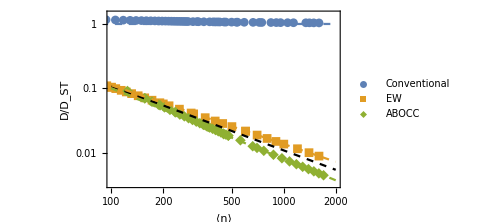

```mathematica
plot1=Show[
ListLogLogPlot[{Transpose[{avgNAll[[All,2]],normalTbAll[[All,2]]}],dataDSGAll,aboccPlotData3}
,Frame->True,FrameStyle->Directive[Black,FontSize->16,FontFamily->"Cambria"]
,FrameLabel->{"⟨n⟩","D/D_ST"}
,ImageSize->5 72
(*,Joined->True*)
,PlotMarkers->Automatic
,PlotLegends->(Style[#,Black,16,FontFamily->"Cambria"]&/@{"Conventional","EW","ABOCC"})
,PlotRange->{{100,2000},All}
,ImageSize->6.0 72],
Plot[(ftABOCC[0]+ftDSG[0])/2-1x,{x,Log[50],Log[2000]},PlotStyle->{Dashed,Black},PlotRange->Full],
Plot[{Log[1.0+0.0 x],ftDSG[x],ftABOCC[x]},{x,Log[50],Log[2000]},PlotStyle->Dashed,PlotRange->Full]
]
```

# Generating Fig 2

```mathematica
Γnl = 5.0;
```

```mathematica
int=Interpolation[{#[[1]],#[[3]]}&/@minLinewidth]
```

InterpolatingFunction[…]

```mathematica
fit=LinearModelFit[Log[{#[[1]],Exp[#[[3]]]}]&/@minLinewidth,x,x]
```

```mathematica
sampling[nMax_]:=Module[{co1,co2},
minLambda=Exp[int[nMax]];
co1=Range[minLambda/2,3/2 minLambda,minLambda/10];
co1=Log[co1[[;;-2]]];

co2 = Range[ Log[3/2 minLambda],Log[(10 Γnl)/nMax],(Log[(10 Γnl)/nMax]-Log[3/2 minLambda])/19];
Return[Join[co1,co2]];
]
```

```mathematica
(*Generate adaptive sampling for the plots*)
sampling2[nMax_]:=Module[{co1,co2,co3},
minLambda=Exp[fit[Log[nMax]]];
co1=Range[minLambda/2,3/2 minLambda,minLambda/10];
co1=Log[co1[[;;-2]]];

co2 = Range[ Log[3/2 minLambda],Log[(10 Γnl)/nMax],(Log[(10 Γnl)/nMax]-Log[3/2 minLambda])/19];

co3=Range[0.8minLambda,1.2minLambda,(0.4 minLambda)/19];
Return[Sort[Join[co1,co2,Log[co3]]]];
]
```

```mathematica
searchGammaNew[γLog_?NumericQ,nmax_?IntegerQ]:=Module[{λa,γ},
γ=Exp[γLog];
(*Print[γ];*)
λa= 2 γ nmax + 2 Γnl;
superOp =1000 √(λa Γnl) hsysOp+γ cavityDecay+λa pumpSO+Γnl cavityDecayNL;
{eigenvalues,eigenstates}=Eigensystem[superOp,-3];
steady=Partition[projector.SparseArray[Chop[eigenstates[[-1]]]],Length[aOp]];
steady=steady/Tr[steady];
distribute=Diagonal[Sum[(sBasis[[j]].steady.sBasis[[j]]ᵀ),{j,Length[sBasis]}]];
nMean = Chop[Tr[aOpᵀ.aOp.steady]];
lw= Abs[eigenvalues[[-2]]]/((Γnl + γ Abs[nMean])/(4 Abs[nMean]^2));
AppendTo[dataTemp,{λa, γ,eigenvalues,nMean,Chop[distribute],Chop[γ/(4 Tr[aOpᵀ.aOp.steady])],lw}];
Return[lw]
]
```

```mathematica
nMaxList=Join[Range[100,1000,100],Range[1200,1600,200]]
```

```mathematica
nListE=Range[1000,100,-100]
```

{1000,900,800,700,600,500,400,300,200,100}

```mathematica
sweepLW={};
record={};
Monitor[

Do[
dataTemp={};
coord = sampling2[nmax];

Get[FileNameJoin[{saveDir,"DSG_super_ops_"<>ToString[nmax]<>".m"}]];
indexL=selectElement[Length[aOp]];
projector = makeProj[indexL,Length[aOp]];
projectorD=Transpose[projector];


tbTemp = Table[
searchGammaNew[coord[[k]],nmax]
,{k,Length[coord]}];

AppendTo[sweepLW,Transpose[{Exp[coord],tbTemp}]];

AppendTo[record,dataTemp];

,{nmax,1000,100,-100}];

,{nmax,k}]
```

```mathematica
pltDataE=Table[{(#[[1]] nListE[[j]])/Γnl,#[[2]]}&/@sweepLW[[j]],
{j,Length[nListE],1,-1}];
```

```mathematica
pltAll = Show[ListLogLogPlot[pltDataE[[;;;;2]]
,Joined->True
,Frame->True,FrameStyle->Directive[Black,FontSize->16,FontFamily->"Cambria"]
,FrameLabel->{"Γ_cn_p/Γ_e","D/D_ST"}
,PlotRange->{{0.01,10},{0.01,0.5}}
,ImageSize->6 72
,AspectRatio->0.8
,PlotLegends->(Style["n_p = "<>ToString[#],Black,16,FontFamily->"Cambria"]&/@Reverse[nListE][[;;;;2]])
]
,LogLogPlot[1/2 x/(1+x),{x,0,10},PlotRange->Full,PlotStyle->Directive[Black,Dashed,Opacity[0.8]]]
]
```

```mathematica
pltDataE=Table[{(#[[1]] nListE[[j]])/Γnl,#[[2]]}&/@sweepLW[[j]],
{j,Length[nListE],1,-1}];
```

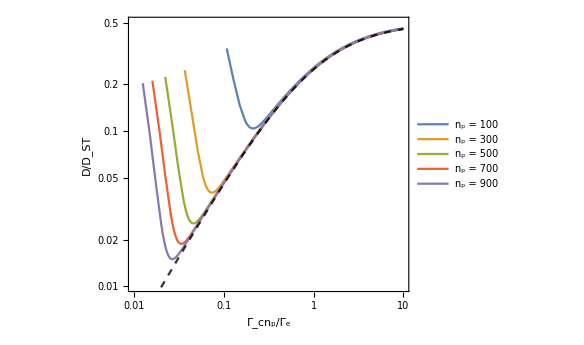

```mathematica
pltAll = Show[ListLogLogPlot[pltDataE[[;;;;2]]
,Joined->True
,Frame->True,FrameStyle->Directive[Black,FontSize->16,FontFamily->"Cambria"]
,FrameLabel->{"Γ_cn_p/Γ_e","D/D_ST"}
,PlotRange->{{0.01,10},{0.01,0.5}}
,ImageSize->6 72
,AspectRatio->0.8
,PlotLegends->(Style["n_p = "<>ToString[#],Black,16,FontFamily->"Cambria"]&/@Reverse[nListE][[;;;;2]])
]
,LogLogPlot[1/2 x/(1+x),{x,0,10},PlotRange->Full,PlotStyle->Directive[Black,Dashed,Opacity[0.8]]]
]
```

```mathematica
pltDataE2=Table[

Transpose[{Re[(sweepLW[[j,All,1]]record[[j,All,4]])/Γnl],sweepLW[[j,All,2]]}],
{j,Length[nListE],1,-1}];
```

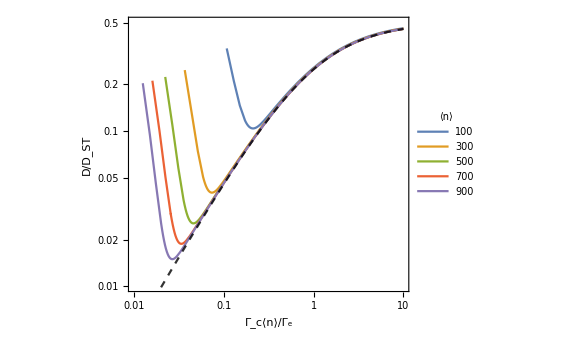

```mathematica
pltAll = Show[ListLogLogPlot[pltDataE2[[;;;;2]]
,Joined->True
,Frame->True,FrameStyle->Directive[Black,FontSize->16,FontFamily->"Cambria"]
,FrameLabel->{"Γ_c⟨n⟩/Γ_e","D/D_ST"}
,PlotRange->{{0.01,10},{0.01,0.5}}
,ImageSize->6 72
,AspectRatio->0.8
(*,PlotLegends->(Style["⟨n⟩ = "<>ToString[#],Black,16,FontFamily->"Cambria"]&/@Reverse[nListE][[;;;;2]])*)
,PlotLegends->LineLegend[Reverse[nListE][[;;;;2]],LegendLabel->"⟨n⟩",LabelStyle->Directive[Black,16,FontFamily->"Cambria"],LegendFunction->"Frame"]
]
,LogLogPlot[1/2 x/(1+x),{x,0,10},PlotRange->Full,PlotStyle->Directive[Black,Dashed,Opacity[0.8]]]
]
```

```mathematica
nListE=Range[1000,100,-100]
```

{1000,900,800,700,600,500,400,300,200,100}

```mathematica
newCoord3=Table[
{ 30.0/nListE[[j]]^2,minLWTb[[-3-j,3]],10 minLWTb[[-3-j,3]],10 Γnl/nListE[[j]]}
,{j,Length[nListE]}]
```

{{0.00003,0.000121622,0.00121622,0.05},{0.000037037,0.000148885,0.00148885,0.0555556},{0.000046875,0.000186558,0.00186558,0.0625},{0.0000612245,0.000241144,0.00241144,0.0714286},{0.0000833333,0.000324226,0.00324226,0.0833333},{0.00012,0.000460319,0.00460319,0.1},{0.0001875,0.000707062,0.00707062,0.125},{0.000333333,0.00123223,0.0123223,0.166667},{0.00075,0.00270571,0.0270571,0.25},{0.003,0.0105924,0.105924,0.5}}

```mathematica
sweepLW5={};
record5={};
Monitor[

Do[
dataTemp={};
nmax=nListE[[j]];
coord =newCoord3[[j]];

nmax = nListE[[j]];
Get[FileNameJoin[{saveDir,"DSG_super_ops_"<>ToString[nmax]<>".m"}]];
indexL=selectElement[Length[aOp]];
projector = makeProj[indexL,Length[aOp]];
projectorD=Transpose[projector];

tbTemp = Table[
searchGammaNew[Log[coord[[k]]],nmax]
,{k,Length[coord]}];

AppendTo[sweepLW5,Transpose[{Exp[coord],tbTemp}]];

AppendTo[record5,dataTemp];

,{j,Length[nListE]}];

,{nmax,k}]
```

```mathematica
pltData1=Table[Transpose[{(Range[Length[#]]-1)/nListE[[j]],#/Max[#]}]&@record5[[j,1,5]],{j,Length[record5],1,-1}];
```

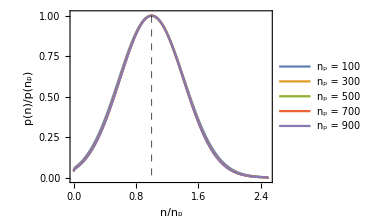

```mathematica
plt1 = ListPlot[pltData1[[;;;;2]]
,Frame->True,FrameLabel->{"n/n_p","p(n)/p(n_p)"}
,FrameStyle->Directive[Black,FontSize->16,FontFamily->"Cambria"]
,PlotRange->{{0,2.5},{-0.01,1.01}}
,Joined->True
,AspectRatio->0.75
,GridLines->{{{1.0,Directive[Black,Dashed,Opacity[1]]}},None}
,PlotLegends->(Style["n_p = "<>ToString[#],Black,16,FontFamily->"Cambria"]&/@Reverse[nListE][[;;;;2]])
,ImageSize->4 72]
```

```mathematica
pltData1p=Table[
nAvg = Total[(Range[Length[#]]-1)#&@record5[[j,1,5]]];
Transpose[{(Range[Length[#]]-1)/nAvg,#/(#[[Round[nAvg]+1]])}]&@record5[[j,1,5]],{j,Length[record5],1,-1}];
```

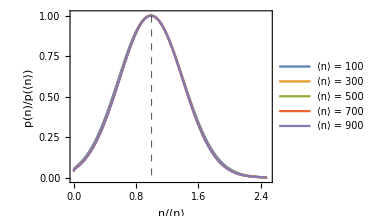

```mathematica
plt1p = ListPlot[pltData1p[[;;;;2]]
,Frame->True,FrameLabel->{"n/⟨n⟩","p(n)/p(⟨n⟩)"}
,FrameStyle->Directive[Black,FontSize->16,FontFamily->"Cambria"]
,PlotRange->{{0,2.5},{-0.01,1.01}}
,Joined->True
,AspectRatio->0.75
,GridLines->{{{1.0,Directive[Black,Dashed,Opacity[1]]}},None}
,PlotLegends->(Style["⟨n⟩ = "<>ToString[#],Black,16,FontFamily->"Cambria"]&/@Reverse[nListE][[;;;;2]])
,ImageSize->4 72]
```

```mathematica
pltData2p=Table[
nAvg = Total[(Range[Length[#]]-1)#&@record5[[j,2,5]]];
Transpose[{(Range[Length[#]]-1)/nAvg,#/(#[[Round[nAvg]+1]])}]&@record5[[j,2,5]],{j,Length[record5],1,-1}];
```

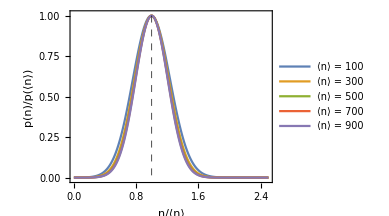

```mathematica
plt2p = ListPlot[pltData2p[[;;;;2]]
,Frame->True,FrameLabel->{"n/⟨n⟩","p(n)/p(⟨n⟩)"}
,FrameStyle->Directive[Black,FontSize->16,FontFamily->"Cambria"]
,PlotRange->{{0,2.5},{-0.01,1.01}}
,Joined->True
,AspectRatio->0.75
,GridLines->{{{1.0,Directive[Black,Dashed,Opacity[1]]}},None}
,PlotLegends->(Style["⟨n⟩ = "<>ToString[#],Black,16,FontFamily->"Cambria"]&/@Reverse[nListE][[;;;;2]])
,ImageSize->4 72]
```

```mathematica
pltData3p=Table[
nAvg = Total[(Range[Length[#]]-1)#&@record5[[j,3,5]]];
Transpose[{(Range[Length[#]]-1)/nAvg,#/(#[[Round[nAvg]+1]])}]&@record5[[j,3,5]],{j,Length[record5],1,-1}];
```

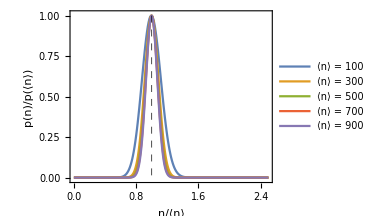

```mathematica
plt3p = ListPlot[pltData3p[[;;;;2]]
,Frame->True,FrameLabel->{"n/⟨n⟩","p(n)/p(⟨n⟩)"}
,FrameStyle->Directive[Black,FontSize->16,FontFamily->"Cambria"]
,PlotRange->{{0,2.5},{-0.01,1.01}}
,Joined->True
,AspectRatio->0.75
,GridLines->{{{1.0,Directive[Black,Dashed,Opacity[1]]}},None}
,PlotLegends->(Style["⟨n⟩ = "<>ToString[#],Black,16,FontFamily->"Cambria"]&/@Reverse[nListE][[;;;;2]])
,ImageSize->4 72]
```

```mathematica
pltData4p=Table[
nAvg = Total[(Range[Length[#]]-1)#&@record5[[j,4,5]]];
Transpose[{(Range[Length[#]]-1)/nAvg,#/(#[[Round[nAvg]+1]])}]&@record5[[j,4,5]],{j,Length[record5],1,-1}];
```

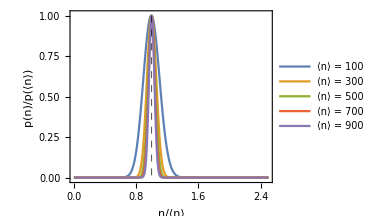

```mathematica
plt4p = ListPlot[pltData4p[[;;;;2]]
,Frame->True,FrameLabel->{"n/⟨n⟩","p(n)/p(⟨n⟩)"}
,FrameStyle->Directive[Black,FontSize->16,FontFamily->"Cambria"]
,PlotRange->{{0,2.5},{-0.01,1.01}}
,Joined->True
,AspectRatio->0.75
,GridLines->{{{1.0,Directive[Black,Dashed,Opacity[1]]}},None}
,PlotLegends->(Style["⟨n⟩ = "<>ToString[#],Black,16,FontFamily->"Cambria"]&/@Reverse[nListE][[;;;;2]])
,ImageSize->4 72]
```

```mathematica
plt4Width = Transpose[{√(1.0 nListE),√(Total[(Range[Length[#]]-1)^2#]-Total[(Range[Length[#]]-1)#]^2)&/@record5[[All,4,5]]}]
```

{{31.6228,33.1699},{30.,31.4681},{28.2843,29.6689},{26.4575,27.7533},{24.4949,25.6952},{22.3607,23.4573},{20.,20.9821},{17.3205,18.1727},{14.1421,14.8408},{10.,10.5}}

```mathematica
lf= LinearModelFit[plt4Width,x,x]
```

FittedModel[0.0135639+1.04847 x]

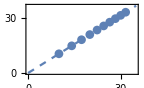

```mathematica
plt4Insert=Show[
ListPlot[plt4Width
,PlotMarkers->Automatic
,Axes->None
,Frame->True,FrameStyle->Directive[Black,FontSize->12,FontFamily->"Cambria"]
,FrameLabel->{Style["√n_p",12],Style["Δn",12]}
,FrameTicks->{{{0,15,30},None},{{0,15,30},None}}
,ImageSize->2.0 72
]
,Plot[lf[x],{x,0,35},PlotStyle->Dashed],PlotRange->All]
```

# Fig. 3 plots

```mathematica
ϕ0 = Quantity["ReducedPlanckConstant"]/(2Quantity["ElementaryCharge"])
```

1/2 ℏ/e

```mathematica
bracketN[m_?IntegerQ,n_?IntegerQ]:=Module[{res},
If[n>m,Return[0]];
res = 1;
Do[
res *= m-j
,{j,0,n-1}];
Return[res]
]
```

```mathematica
phit=UnitConvert[√((Quantity["PlanckConstant"]Quantity[7.5,"GHz"])/(ϕ0 Quantity[0.1,"μA"]))]
```

0.388589

```mathematica
bigPhi = Exp[-UnitConvert[1./ϕ0^2(Quantity["ReducedPlanckConstant"]Quantity[50,"Ohms"])/(4 π)]]
```

0.996133

```mathematica
phic =Sqrt[ UnitConvert[1./ϕ0^2(Quantity["ReducedPlanckConstant"]Quantity[50,"Ohms"])/2]]
expPhic = Exp[-1/2 UnitConvert[1./ϕ0^2(Quantity["ReducedPlanckConstant"]Quantity[50,"Ohms"])/2]]
```

0.156017

0.987903

```mathematica
Aelem[m_?IntegerQ,rac_?NumericQ,zc_?NumericQ]:=Module[{ϕc,expϕc},
ϕc =Sqrt[ UnitConvert[1./ϕ0^2(Quantity["ReducedPlanckConstant"]Quantity[zc,"Ohms"])/2]];
expϕc=Exp[-1/2 UnitConvert[1./ϕ0^2(Quantity["ReducedPlanckConstant"]Quantity[zc,"Ohms"])/2]];
Quiet[ ϕc √(m+1) (bigPhi Exp[-ϕc^2/2]Sum[(-1)^n ϕc^(2n)/(1.0 Factorial[n] Factorial[n+1])bracketN[m,n],{n,0,m}]+2 rac)]
]
```

```mathematica
selectElement[dim_?IntegerQ]:=Module[{center,first,second,third,fourth,fifth},
center =Transpose[{Range[dim],Range[dim]}];
first=Join[ Transpose[{Range[dim-1],Range[2,dim]}],Transpose[{Range[2,dim],Range[dim-1]}]];

second =Join[Transpose[{Range[dim-2],Range[3,dim]}],Transpose[{Range[3,dim],Range[dim-2]}]];

third = Join[Transpose[{Range[dim-3],Range[4,dim]}],Transpose[{Range[4,dim],Range[dim-3]}]];

fourth = Join[Transpose[{Range[dim-4],Range[5,dim]}],Transpose[{Range[5,dim],Range[dim-4]}]];

fifth = Join[Transpose[{Range[1,dim-5,2],Range[6,dim,2]}], Transpose[{Range[6,dim,2],Range[1,dim-5,2]}]];

Return[Join[center,first,second,third,fourth,fifth]]
]
```

```mathematica
makeProj[indexList_,dim_?IntegerQ]:=Module[{},
projRL = ParallelTable[
{(indexList[[k,1]]-1)dim+indexList[[k,2]],k}->1
,{k,Length[indexList]}
];
projector = SparseArray[projRL,{dim*dim,Length[indexList]}];
Return[projector]
]
```

```mathematica
updateABOCCopsNew[zc_?NumericQ]:=Module[{},
m0=Round[fit[1/zc]];
maxN = Round[2.5 m0];


aTrunc =Floor[maxN];

aopRL =Table[{j,j+1}->√(1. (j)),{j,1,aTrunc}];
aop=SparseArray[aopRL,{(aTrunc+1), (aTrunc+1)}];
iaop = SparseArray[IdentityMatrix[Length[aop]]];

{sx,sy,sz,si} = PauliMatrix[#]&/@Range[4];
sp = 1/2(sx+ⅈ sy);
sm = 1/2(sx-ⅈ sy);
{sX,sY,sZ,sI,sP,sM} = KroneckerProduct[iaop,#]&/@{sx,sy,sz,si,sp,sm};
aOp=KroneckerProduct[aop,IdentityMatrix[2]];
iOp=SparseArray[IdentityMatrix[Length[aOp]]];

eopRL =Table[{j,j+1}->1,{j,1,aTrunc}];
eop=SparseArray[eopRL,{ (aTrunc+1), (aTrunc+1)}];
eOp=KroneckerProduct[eop,SparseArray[IdentityMatrix[2]]];

indexL=selectElement[Length[aOp]];
projector = makeProj[indexL,Length[aOp]];
projectorD=Transpose[projector];

(*aBasis=Table[
SparseArray[KroneckerProduct[SparseArray[i->1,{Length[aop]}],SparseArray[IdentityMatrix[2]]]]
,{i,Length[aop]}];*)
sBasis={SparseArray[KroneckerProduct[IdentityMatrix[Length[aop]],{1,0}]],
SparseArray[KroneckerProduct[IdentityMatrix[Length[aop]],{0,1}]]};

phit=UnitConvert[√((Quantity["PlanckConstant"]Quantity[7.5,"GHz"])/(ϕ0 Quantity[0.1,"μA"]))];
phic =Sqrt[ UnitConvert[1./ϕ0^2(Quantity["ReducedPlanckConstant"]Quantity[zc,"Ohms"])/2]];

bigPhi = Exp[-UnitConvert[1./ϕ0^2(Quantity["ReducedPlanckConstant"]Quantity[50,"Ohms"])/(4 π)]];
expPhic = Exp[-1/2 UnitConvert[1./ϕ0^2(Quantity["ReducedPlanckConstant"]Quantity[zc,"Ohms"])/2]];

generateAops[phic,bigPhi,0.418,maxN,m0];
AopcD=Aopcᵀ;

AOpc= KroneckerProduct[Aopc,SparseArray[IdentityMatrix[2]]];
AOpcD=KroneckerProduct[AopcD,SparseArray[IdentityMatrix[2]]];
hac = AOpc.sP + AOpcD.sM;
HacSO =-ⅈ ( projectorD.combineOps[hac,iOp].projector-projectorD.combineOps[iOp,hac].projector);
pumpSO = -1/2(projectorD.combineOps[sM.sP,iOp].projector+projectorD.combineOps[iOp,sM.sP].projector-2projectorD.combineOps[sP,sM].projector);
normalLossSO = -1/2(projectorD.combineOps[aOpᵀ.aOp,iOp].projector+projectorD.combineOps[iOp,aOpᵀ.aOp].projector-2 projectorD.combineOps[aOp,aOpᵀ].projector);
lossSO = -1/2(projectorD.combineOps[AOpcᵀ.AOpc,iOp].projector+projectorD.combineOps[iOp,AOpcᵀ.AOpc].projector-2 projectorD.combineOps[AOpc,AOpcᵀ].projector);
Speak["Operators are updated."]
]
```

```mathematica
findMinN[zc_?NumericQ]:=Module[{tbAelem,tbAelemDiff,pos},
tbAelem = ParallelTable[ Aelem[j,0.418,zc],{j,0,3000}];
tbAelemDiff=tbAelem[[2;;]]-tbAelem[[;;-2]];

pos=Position[tbAelemDiff,Min[tbAelemDiff]][[1,1]];

Return[{pos+1,tbAelem}]
]
```

```mathematica
{pos1,aList1}=findMinN[50];
```

```mathematica
pos1
```

128

```mathematica
Monitor[
aListTable=Table[
{pos,aList}=findMinN[zc];
{pos,aList}
,{zc,{50,40,30,20,15,10}}];
,zc]
```

```mathematica
aPltData = Table[
Transpose[{Range[Length[aListTable[[j,2]]]]/aListTable[[j,1]],aListTable[[j,2]]}]
,{j,Length[aListTable]}];
```

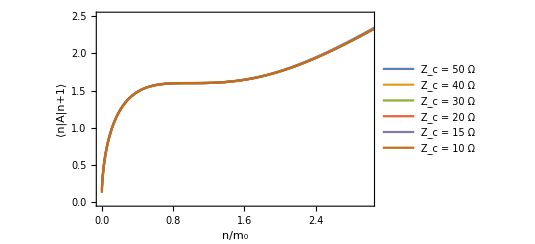

```mathematica
ListPlot[aPltData,PlotRange->{{0,3},{0,2.5}},Joined->True,Frame->True,FrameStyle->Directive[Black,FontSize->16,FontFamily->"Times New Roman"]
,FrameLabel->{"n/m_0","⟨n|A|n+1⟩"}
,PlotLegends->(Style["Z_c = "<>ToString[#]<>" Ω",Black,16,FontFamily->"Times New Roman"]&/@{50,40,30,20,15,10})
,ImageSize->5.5 72]
```

```mathematica
aPltData2= Table[
Transpose[{Range[Length[aListTable[[j,2]]]]/aListTable[[j,1]],Re[aListTable[[j,2]]/aListTable[[j,2,aListTable[[j,1]]]]]}]
,{j,Length[aListTable]}];
```

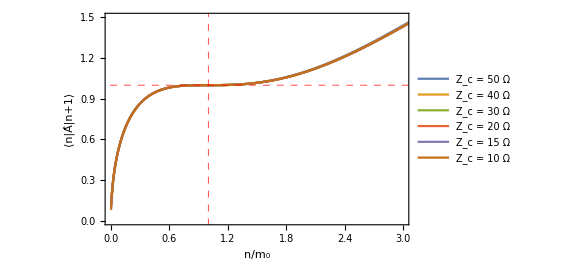

```mathematica
plot3Main=ListPlot[aPltData2,PlotRange->{{0,3},{0,1.5}},Joined->True,Frame->True,FrameStyle->Directive[Black,FontSize->22,FontFamily->"Cambria"]
,FrameLabel->{"n/m_0","⟨n|Â|n+1⟩"}
,PlotLegends->(Style["Z_c = "<>ToString[#]<>" Ω",Black,22,FontFamily->"Cambria"]&/@{50,40,30,20,15,10})
,GridLines->{{{1.0,Directive[Dashed,Red,Opacity[1]]}},{{1.0,Directive[Dashed,Red,Opacity[1]]}}}
,ImageSize->6 72]
```

```mathematica
Get[FileNameJoin[{saveDir,"ABOCC_m0_vs_Zc_data.m"}]];
```

```mathematica
fit=LinearModelFit[{(#[[1]])^-1,#[[2]]}&/@posTb,x,x]
```

FittedModel[0.514286+6356.43 x]

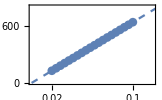

```mathematica
plot3Insert=Show[
ListPlot[{(#[[1]])^-1,#[[2]]}&/@posTb
,Frame->True,FrameStyle->Directive[Black,FontSize->16,FontFamily->"Cambria"]
,FrameLabel->{"1/Z_c (Ω^-1)","m_0"}
,ImageSize->2.25 72
,PlotMarkers->Automatic
,PlotRange->{{0,0.12},{0,800}}
,FrameTicks->{{{0,300,600},Automatic},{{0.02,0.06,0.1},Automatic}}]
,Plot[fit[x],{x,0,0.15},PlotStyle->Dashed]
]
```

```mathematica
tempFun3[lambda_?NumericQ,gr_?NumericQ]:=Module[{γ,g},

γ=1.0;
g=gr lambda/2 √(γ/(lambda - 2 γ));
superOp = lambda pumpSO + γ lossSO +  g HacSO;

{ev,es} = Eigensystem[superOp,-3];

steady = SparseArray[Chop[Partition[projector.es[[-1]],Length[aOp]]]];
steady = steady/Tr[steady];

rate = Tr[AOpc.steady.AOpcD];
nAvg = Tr[aOpᵀ.aOp.steady];
Return[{lambda,gr g,nAvg,rate,Abs[ev[[-2]] ]/(rate/(4 nAvg^2))}]
]
```

```mathematica
tempFun4[lambda_?NumericQ,g_?NumericQ]:=Module[{γ},

γ=1.0;
(*g=gr lambda/2 √(γ/(lambda - 2 γ));*)
superOp = lambda pumpSO + γ lossSO +  g HacSO;

{ev,es} = Eigensystem[superOp,-2];

steady = SparseArray[Chop[Partition[projector.es[[-1]],Length[aOp]]]];
steady = steady/Tr[steady];

rate = Tr[AOpc.steady.AOpcD];
nAvg = Tr[aOpᵀ.aOp.steady];
Return[{lambda,g,Abs[nAvg],Abs[rate],Abs[ev[[-2]] ]/Abs[rate/(4 nAvg^2)]}]
]
```

```mathematica
Get[FileNameJoin[{saveDir,"ABOCC_SO_m0_"<>ToString[1600]<>".m"}]];
indexL=selectElement[Length[aOp]];
projector = makeProj[indexL,Length[aOp]];
projectorD=Transpose[projector];
```

```mathematica
g0=3.5/2 √(1.0/(3.5-2));
```

```mathematica
mesh=Flatten[
Table[
{x,y}
,{x,3.4,3.7,0.01}
,{y,0.99 g0, 1.01 g0,0.00025 g0}]
,1];
Length[mesh]
```

2511

```mathematica
sweepLW = ParallelTable[
{lambda,g1}=mesh[[j]];
tempFun4[lambda,g1]
,{j,Length[mesh]}];
```

$Aborted

```mathematica
SortBy[sweepLW,#[[5]]&][[;;5]]
```

{{3.58,1.42458,1659.63,1.0006,0.00434046},{3.56,1.42565,1657.63,1.00057,0.0043406},{3.6,1.42351,1656.54,1.00055,0.00434066},{3.53,1.42744,1657.54,1.00056,0.00434213},{3.63,1.42208,1655.6,1.00054,0.00434229}}

```mathematica
pt={SortBy[sweepLW,#[[5]]&][[1,2]],SortBy[sweepLW,#[[5]]&][[1,1]]}
```

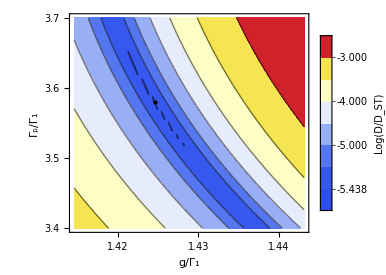

```mathematica
plt1New=Show[
ListContourPlot[{#[[2]],#[[1]],Log[#[[5]]]}&/@sweepLW,ColorFunction->"TemperatureMap",Contours->{-5.43979,-5.438,-5.3,-5,-4.5,-4,-3.5,-3}
,Frame->True
,FrameStyle->Directive[Black,FontSize->22,FontFamily->"Cambria"]
,FrameLabel->{"g/Γ_1","Γ_p/Γ_1"}
,ImageSize->4.5 72
,FrameTicks->{{{3.4,3.5,3.6,3.7},Automatic},{{1.42,1.43,1.44},Automatic}}
,AspectRatio->0.85
,PlotLegends->Placed[BarLegend[Automatic,LabelStyle->Directive[Black,22,FontFamily->"Cambria"],LegendLabel->Style["Log(D/D_ST)",Italic]],Right]]
,Graphics[{Black,PointSize[Large],Point[pt]}]
]
```

```mathematica
tempFun5[lambda_?NumericQ,g_?NumericQ]:=Module[{γ},

γ=1.0;
(*g=gr lambda/2 √(γ/(lambda - 2 γ));*)
superOp = lambda pumpSO + γ lossSO +  g HacSO;

{ev,es} = Eigensystem[superOp,-2];

steady = SparseArray[Chop[Partition[projector.es[[-1]],Length[aOp]]]];
steady = steady/Tr[steady];
steadyR = sBasis[[1]].steady.sBasis[[1]]ᵀ+sBasis[[2]].steady.sBasis[[2]]ᵀ;

rate = Tr[AOpc.steady.AOpcD];
nAvg = Tr[aOpᵀ.aOp.steady];
Return[{lambda,g,Abs[nAvg],Abs[rate],Abs[ev[[-2]] ]/Abs[rate/(4 nAvg^2)],Diagonal[steadyR]}]
]
```

```mathematica
dist1600=tempFun5[#2,#1]&@@pt;
```

```mathematica
mesh2=Flatten[
Table[
{x,y}
,{x,3.4,3.7,0.05}
,{y,0.995 g0, 1.005 g0,0.00025 g0}]
,1];
Length[mesh2]
```

287

```mathematica
Get[FileNameJoin[{sopDir,"ABOCC_SO_m0_"<>ToString[1500]<>".m"}]];
indexL=selectElement[Length[aOp]];
projector = makeProj[indexL,Length[aOp]];
projectorD=Transpose[projector];
```

```mathematica
sweepLW1500 = ParallelTable[
{lambda,g1}=mesh2[[j]];
tempFun4[lambda,g1]
,{j,Length[mesh2]}];
```

```mathematica
minPoint=Table[
sel = Select[sweepLW1500,#[[1]]==x&];
SortBy[sel,#[[-1]]&][[1]]
,{x,3.4,3.7,0.05}]
```

{{3.4,1.43601,1476.62,0.999275,0.00506291},{3.45,1.43316,1557.7,1.00063,0.00465579},{3.5,1.42958,1564.79,1.00075,0.00465266},{3.55,1.42637,1562.39,1.00072,0.00464539},{3.6,1.42351,1552.62,1.00055,0.00464308},{3.65,1.42172,1585.8,1.00112,0.00470275},{3.7,1.42172,1707.59,1.0034,0.00641708}}

```mathematica
sweepLW1500 = ParallelTable[
{lambda,g1}=mesh[[j]];
tempFun4[lambda,g1]
,{j,Length[mesh]}];
```

```mathematica
dist1500=tempFun5[#1,#2]&@@SortBy[sweepLW1500,#[[5]]&][[1]];
```

```mathematica
Get[FileNameJoin[{sopDir,"ABOCC_SO_m0_"<>ToString[1400]<>".m"}]];
indexL=selectElement[Length[aOp]];
projector = makeProj[indexL,Length[aOp]];
projectorD=Transpose[projector];
```

```mathematica
dist1400=tempFun5[#1,#2]&@@SortBy[sweepLW1500,#[[5]]&][[1]];
```

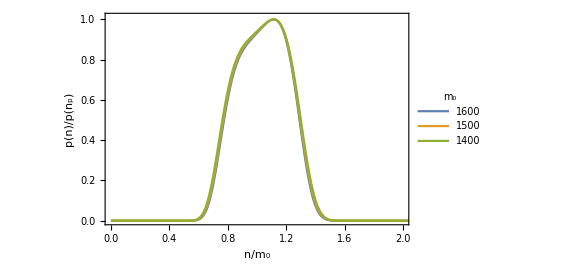

```mathematica
plt2New=ListPlot[{Transpose[{(Range[Length[dist1600[[-1]]]]-1)/1600,Abs[dist1600[[-1]]]/Max[Abs[dist1600[[-1]]]]}],Transpose[{(Range[Length[dist1500[[-1]]]]-1)/1500,Abs[dist1500[[-1]]]/Max[Abs[dist1500[[-1]]]]}],Transpose[{(Range[Length[dist1400[[-1]]]]-1)/1400,Abs[dist1400[[-1]]]/Max[Abs[dist1400[[-1]]]]}]}
,Joined->True
,PlotRange->{{0,2},{0,1.01}}
,Frame->True,FrameStyle->Directive[Black,FontSize->22,FontFamily->"Cambria"]
,FrameLabel->{"n/m_0","p(n)/p(n_p)"}
,ImageSize->6 72
,PlotLegends->LineLegend[{1600,1500,1400},LegendLabel->"m_0",LabelStyle->Directive[Black,22,FontFamily->"Cambria"],LegendFunction->"Frame"]
]
```